```mathematica
Light Scattering by a Spherical Particle for Mathematica 8
```

0.0000216 by for Light Mathematica Particle Scattering Spherical

## Usage Notes

Date: 		Last Modification: 05/17/12
		Mathematica Version 8.0.10
		
Author:	Guy Mongelli
	  
	  	University of Rochester
	  	Dept. of Chemical Engineering
	  	Rochester, NY 14627
	  	mongelli@che.rochester.edu

Application:
	This notebook calculates and plots the scattering, absorption, and extinction properties of a spherical particle of known refractive index in a suspending medium, also of known index.  The particle is illuminated by an unpolarized or linearly polarized  plane wave of unit amplitude.  The code derives from expositions of the problem in Principles of Optics by Born and Wolf, Absorption and Scattering of Light by Small Particles by Bohren and Huffman, and Light Scattering by Small Particles  by H.C. van de Hulst.  It is capable of calculating the spectral properties of such a particle if the dispersion of both the particle and suspending medium are known.  Similarly, absorptive suspending media are allowable when the complex refractive index is provided.

Layout:
	Parameters such as cross sections, phase functions, efficiency factors, etc. may be calculated and displayed.

## Model Parameters

This section is devoted to entering the known parameters for the problem (i.e., complex indices of refraction, wavelength of the illuminating radiation, sphere radius, etc.).  Subscripts of 1 correspond to the embedding medium and subscripts of 2 represent the sphere.  It is assumed by H.C. van de Hulst that neither the medium nor the particle is magnetic (or at very least they have the same permeability).  Notice that the imaginary part of the refractive index is represented by a lower case k, and that capital K represents the wave number.  Finally, it would be more efficient to assign the parameter values (lambda of excitation, radius, real and imaginary index) using rewrite rules in the actual function calls but I've presented them as constants because this format is more readable.

```mathematica
Vary n2 from .2 to .1 and k2 from 1.5 to 5.5
```

0.165 and from^2 k2 n2 to^2 Vary

```mathematica
Subscript[n, 1] = 1.4;                             (* Real part of refractive index of medium *)
Subscript[n, 2] =.2;            (* Real part of refractive index of scatterer *)
Subscript[k, 1] = 0*10^-2 ;                (* Imag"inary part of refractive index of medium *)
Subscript[k, 2] = 3.6;                 (* Imaginary part of refractive index of scatterer *)
Subscript[λ, 0] = 544543 * 10^-6;   (* Vacuum wavelength in μm *)
r =.1             (*Sphere radius in μm *);
```

Required derived quantities for given parameter set.

```mathematica
Subscript[m, 1] = Subscript[n, 1] + I Subscript[k, 1]  ;               (* Complex refractive index of medium *)
Subscript[m, 2] = Subscript[n, 2] + I Subscript[k, 2]  ;             (* Complex refractive index of scatterer *)
Subscript[m, Rel] = (Subscript[n, 2] + I Subscript[k, 2])/(Subscript[n, 1] + I Subscript[k, 1]) ;          (* Relative refractive index between scatterer and medium *)
Subscript[λ, 1] =Subscript[λ, 0]/(Subscript[n, 1] + I Subscript[k, 1]);               (* Wavelength in external medium in μm *)
Subscript[λ, 2] =Subscript[λ, 0]/(Subscript[n, 2] + I Subscript[k, 2]) ;              (* Wavelength inside sphere in μm *)
Subscript[K, 0] =  (2 π)/Subscript[λ, 0];                         (* Wave number in vacuum in μm^-1 *)
Subscript[K, 1] =  (2 π)/Subscript[λ, 1];                         (* Wave number in external medium in μm^-1 *)
Subscript[K, 2] =  (2 π)/Subscript[λ, 2]                          (* Wave number inside the sphere in μm^-1*) ;
```

```mathematica
Subscript[m, 1]            (* Complex refractive index of medium *)
Subscript[m, 2]            (* Complex refractive index of scatterer *)
Subscript[m, Rel]           (* Relative refractive index between scatterer and medium *)
Subscript[λ, 1]               (* Wavelength in external medium in μm *)
Subscript[λ, 2]               (* Wavelength inside sphere in μm *)
Subscript[K, 0]                (* Wave number in vacuum in μm^-1 *)
Subscript[K, 1]                  (* Wave number in external medium in μm^-1 *)
Subscript[K, 2]              (* Wave number inside the sphere in μm^-1*)
```

1.4

0.2+3.6 ⅈ

0.142857+2.57143 ⅈ

0.388959

0.00837758-0.150797 ⅈ

(2000000 π)/544543

16.1538

2.30769+41.5384 ⅈ

Now create the size parameter.  Note there are actually three size parameters defined (as opposed to Bohren and Huffman's single size parameter), two of which are now complex and due to the fact that the external medium may be absorptive.  They come from the paper by Fu and Sun (Applied Optics, Vol. 40, No. 9, 2001,pp. 1354-1361) which explains how to treat a particle in an absorbing medium.  They are used subsequently to determine how many terms are maintained in the series defining the scattered intensity, cross sections, efficiencies, asymmetry factor, etc., and also serve as arguments to the scattering coefficient equations.  They are set up as functions of particle radius so that this may be varied and plots vs. radius (or q parameter) can be examined.

```mathematica
q[a_] := Subscript[K, 0] a
Subscript[q, 1][a_] :=Subscript[K, 1] a 
Subscript[q, 2][a_] :=Subscript[K, 2] a 

Print["The size parameter is ",q[r]//N]
Print["The external size parameter is ",Subscript[q, 1][r]//N]
Print["The internal size parameter is ",Subscript[q, 2][r]//N]
```

The size parameter is 1.15385

The external size parameter is 1.61538

The internal size parameter is 0.230769+4.15384 ⅈ

I use the equation suggested by Wiscombe [Applied Optics, Vol. 19, (1980) page 1505] for obtaining the series solution termination point for a given size parameter.  Since there are now three (two possibly complex) size parameters, I choose the largest of the absolute values of the three as the argument to the equation.  The equation was found to be valid for the range 8 < q < 4200.  For smaller q values, the suggestion is LastTerm = q + 4 q^(1/3) +1.  I don't suggest trying to run the program for very large size parameters due to the resulting long computation times (in fact, anything over q=100 becomes tediously long).

```mathematica
Largest[a_] :=Max[q[a],Abs[Subscript[q, 1][a]],Abs[Subscript[q, 2][a]]]
LastTerm[a_]:= Ceiling[Abs[Largest[a] + 4.05 (Largest[a])^(1/3) +2]] ;
Print["The series termination value is ",LastTerm[r], "."]
```

The series termination value is 13.

## Required function definitions

The following defines a "complex conjugate" function.  This allows the familiar  *  notation to be used later when the complex conjugates of certain functions are required.

```mathematica
SuperStar[ϕ_] := ϕ/.Complex[u_, v_] -> Complex[u, -v]
```

The spherical Bessel, Neumann and Hankel functions are used to represent the radial field dependence.   Boundary conditions at r = 0 and r = ∞  require finite fields and hence the need for all three types of Bessel functions.  We go straight to the Ricatti-Bessel functions here by simply multiplying through by ρ.

```mathematica
ψ[l_,ρ_]:= ρ √(π/(2 ρ))  BesselJ[(l + 1/2),ρ ]                                  (* Ricatti-Bessel function of 1st kind. *)  
ψPrime[l_,ρ_]:=Evaluate[D[ ψ[l,ρ],ρ]] ;                                (* Partial derivative of Ricatti-Bessel function w/r/t ρ. *)
ζ[l_,ρ_]:=ψ[l, ρ] + I ρ √(π/(2 ρ)) BesselY[(l + 1/2),ρ ] ;      (* Ricatti-Hankel function *)
ζPrime[l_,ρ_]:=Evaluate[D[ ζ[l,ρ],ρ]];(* Partial derivative of Ricatti-Hankel function  w/r/t/ ρ *)
```

The associated Legendre functions are used for the azimuthal components of the field.  These are built into Mathematica.  Note that the Mathematica version has a (-1)^min front of the function definition, which Born and Wolf do not have (but make mention of).  Here, m is the separation constant that arises from the separation of variables technique used to solve the wave equation and must equal one for this problem.  Since m = 1, we get a negative sign out front so another one is multiplied out to conform to the actual field.  Then, these are used to construct the "angle function" coefficients π_n and τ_n. They are derived from the Legendre functions as shown below.  Note the final argument to the Legendre polynomial is actually cos(θ).

```mathematica
pi[i_, θ_] :=  LegendreP[i,1,Cos[θ]]/Sin[θ]; 
τ[i_, θ_]:= D[ LegendreP[i,1,Cos[θ]],θ];
```

```mathematica
TableForm[Table[{FullSimplify[pi[l, θ]] },{l,1,5}], TableHeadings-> {Automatic,{"pi[l, q]"} }]
```

| pi[l, q]
1 | -Csc[θ] √(Sin[θ]^2)
2 | -3 Cot[θ] √(Sin[θ]^2)
3 | 3/2 (-5 Cos[θ] Cot[θ]+Csc[θ]) √(Sin[θ]^2)
4 | -5/2 (-3+7 Cos[θ]^2) Cot[θ] √(Sin[θ]^2)
5 | -15/8 (1-14 Cos[θ]^2+21 Cos[θ]^4) Csc[θ] √(Sin[θ]^2)

```mathematica
TableForm[Table[{FullSimplify[D[pi[l, θ],θ]] },{l,1,5}], TableHeadings-> {Automatic,{"pi'[l, q]"} }]
```

| pi'[l, q]
1 | 0
2 | 3 √(Sin[θ]^2)
3 | 15 Cos[θ] √(Sin[θ]^2)
4 | 15/4 (5+7 Cos[2 θ]) √(Sin[θ]^2)
5 | 105/8 (5 Cos[θ]+3 Cos[3 θ]) √(Sin[θ]^2)

```mathematica
TableForm[Table[{FullSimplify[τ[l,θ]] },{l,1,4}], TableHeadings-> {Automatic,{"τ[l, q]"} }]
```

| τ[l, q]
1 | -Cot[θ] √(Sin[θ]^2)
2 | -3 Cos[2 θ] Csc[θ] √(Sin[θ]^2)
3 | 3/2 (11-15 Cos[θ]^2) Cot[θ] √(Sin[θ]^2)
4 | (5 (Sin[θ]+6 Sin[3 θ]-7 Sin[5 θ]))/(8 √(Sin[θ]^2))

```mathematica
TableForm[Table[{FullSimplify[D[τ[l,θ],θ]] },{l,1,4}], TableHeadings-> {Automatic,{"τ'[l, q]"} }]
```

| τ'[l, q]
1 | √(Sin[θ]^2)
2 | 12 Cos[θ] √(Sin[θ]^2)
3 | 3/4 (23+45 Cos[2 θ]) √(Sin[θ]^2)
4 | 5 (15 Cos[θ]+14 Cos[3 θ]) √(Sin[θ]^2)

```mathematica
TableForm[Table[{FullSimplify[ζ[l,θ] ]},{l,1,4}], TableHeadings-> {Automatic,{"ζ[l, q]","ζ'[l, q]"} }]
```

| ζ[l, q]
1 | -(ⅇ^(ⅈ θ) √(1/θ) (ⅈ+θ))/(√θ)
2 | (ⅈ ⅇ^(ⅈ θ) √(1/θ) (-3+θ (3 ⅈ+θ)))/θ^(3/2)
3 | (ⅇ^(ⅈ θ) √(1/θ) (-15 ⅈ+θ (-15+θ (6 ⅈ+θ))))/θ^(5/2)
4 | (√(1/θ) (105+θ (-105 ⅈ+θ (-45+θ (10 ⅈ+θ)))) (-ⅈ Cos[θ]+Sin[θ]))/θ^(7/2)

```mathematica
TableForm[Table[{FullSimplify[ζPrime[l,θ] ]},{l,1,4}], TableHeadings-> {Automatic,{"ζPrime[l, q]"} }]
```

| ζPrime[l, q]
1 | (ⅇ^(ⅈ θ) √(1/θ) (ⅈ+θ-ⅈ θ^2))/θ^(3/2)
2 | (ⅇ^(ⅈ θ) √(1/θ) (6 ⅈ-θ (-6+θ (3 ⅈ+θ))))/θ^(5/2)
3 | (ⅇ^(ⅈ θ) √(1/θ) (45 ⅈ+θ (45+ⅈ θ (-21+θ (6 ⅈ+θ)))))/θ^(7/2)
4 | (ⅇ^(ⅈ θ) √(1/θ) (420 ⅈ+θ (420+θ (-195 ⅈ+θ (-55+θ (10 ⅈ+θ))))))/θ^(9/2)

```mathematica
TableForm[Table[{FullSimplify[ψ[l,q] ]},{l,1,4}], TableHeadings-> {Automatic,{"ψ[l, q]"} }]
```

| ψ[l, q]
1 | (√(1/q) (-q Cos[q]+Sin[q]))/(√q)
2 | -(√(1/q) (3 q Cos[q]+(-3+q^2) Sin[q]))/q^(3/2)
3 | (√(1/q) (q (-15+q^2) Cos[q]+3 (5-2 q^2) Sin[q]))/q^(5/2)
4 | (√(1/q) (5 q (-21+2 q^2) Cos[q]+(105-45 q^2+q^4) Sin[q]))/q^(7/2)

```mathematica
TableForm[Table[{FullSimplify[ψPrime[l,q] ]},{l,1,4}], TableHeadings-> {Automatic,{"ψ[l, q]"} }]
```

| ψ[l, q]
1 | (√(1/q) (q Cos[q]+(-1+q^2) Sin[q]))/q^(3/2)
2 | (√(1/q) (-q (-6+q^2) Cos[q]+3 (-2+q^2) Sin[q]))/q^(5/2)
3 | -(√(1/q) (3 q (-15+2 q^2) Cos[q]+(45-21 q^2+q^4) Sin[q]))/q^(7/2)
4 | (√(1/q) (q (420-55 q^2+q^4) Cos[q]-5 (84-39 q^2+2 q^4) Sin[q]))/q^(9/2)

```mathematica
(* Manipulate[Plot[pi[l,θ],{θ,0,2π}],{l,1,10}]
```

```mathematica
(* Manipulate[Plot[D[pi[l,θ],θ],{θ,.1,2π}],{l,2,10}]
```

```mathematica
(* Manipulate[Plot[ψPrime[l,q],{q,.1,2π}],{l,2,10}]
```

```mathematica
TableForm[N[Table[{ψ[l, q[r]],ψPrime[l, q[r]] , ζ[l, q[r]],ζPrime[l, q[r]]},{l,1,5}],6], TableHeadings-> {Automatic,{"ψ[l, q]","ψ'[l, q]","ζ[l, q]","ζ'[l, q]"} }]
```

| ψ[l, q] | ψ'[l, q] | ζ[l, q] | ζ'[l, q]
1 | 0.387444 | 0.578543 | 0.387444-1.26531 ⅈ | 0.578543+0.691625 ⅈ
2 | 0.0930261 | 0.226198 | 0.0930261-2.88482 ⅈ | 0.226198+3.73506 ⅈ
3 | 0.0156697 | 0.052285 | 0.0156697-11.2356 ⅈ | 0.052285+26.3278 ⅈ
4 | 0.00203658 | 0.00860953 | 0.00203658-65.2778 ⅈ | 0.00860953+215.061 ⅈ
5 | 0.000215649 | 0.0011021 | 0.000215649-497.932 ⅈ | 0.0011021+2092.43 ⅈ

```mathematica
(* Manipulate[Plot[ψ[l,q],{q,.1,2π}],{l,2,10}]
```

```mathematica
(* Manipulate[Plot[ψPrime[l,q],{q,.1,2π}],{l,2,10}]
```

```mathematica
These are complex functions so they are not represented well in the real plane here.  I will need to plot them in the complex plane.
```

```mathematica
(* Manipulate[Plot[Through[{Re,Im}ζ[l,q]],{q,.1,2π}],{l,1,10}]
```

```mathematica
(* Manipulate[Plot[ζPrime[l,q],{q,.1,2π}],{l,2,10}]
```

```mathematica
TableForm[N[Table[{ψ[l, Subscript[q, 1][r]],ψPrime[l, Subscript[q, 1][r]] , ζ[l,Subscript[q, 1][r]],ζPrime[l, Subscript[q, 1][r]]},{l,1,5}],6], TableHeadings-> {Automatic,{"ψ[l, q_1]","ψ'[l, q_1]","ζ[l, q_1]","ζ'[l, q_1]"} }]
```

| ψ[l, q_1] | ψ'[l, q_1] | ζ[l, q_1] | ζ'[l, q_1]
1 | 0.663005 | 0.588574 | 0.663005-0.971414 ⅈ | 0.588574+0.645924 ⅈ
2 | 0.23229 | 0.375408 | 0.23229-1.84863 ⅈ | 0.375408+1.31736 ⅈ
3 | 0.0559884 | 0.128312 | 0.0559884-4.75053 ⅈ | 0.128312+6.97379 ⅈ
4 | 0.0103265 | 0.030418 | 0.0103265-18.737 ⅈ | 0.030418+41.6459 ⅈ
5 | 0.00154506 | 0.00554418 | 0.00154506-99.6415 ⅈ | 0.00554418+289.677 ⅈ

```mathematica
TableForm[N[Table[{ψ[l, Subscript[q, 2][r]],ψPrime[l, Subscript[q, 2][r]] , ζ[l, Subscript[q, 2][r]],ζPrime[l, Subscript[q, 2][r]]},{l,1,5}],6], TableHeadings-> {Automatic,{"ψ[l, q_2]","ψ'[l, q_2]","ζ[l, q_2]","ζ'[l, q_2]"} }]
```

| ψ[l, q_2] | ψ'[l, q_2] | ζ[l, q_2] | ζ'[l, q_2]
1 | -23.4686+5.9456 ⅈ | 6.17022+25.2757 ⅈ | -0.0189088-0.0046578 ⅈ | 0.00496189-0.0197636 ⅈ
2 | -3.94216-13.8522 ⅈ | -16.7145+4.42276 ⅈ | -0.00770187+0.0287156 ⅈ | -0.0324869-0.00912044 ⅈ
3 | 6.58316-2.13849 ⅈ | -2.66577-9.02681 ⅈ | 0.0528541+0.0158144 ⅈ | -0.0212024+0.0661381 ⅈ
4 | 0.963919+2.59292 ⅈ | 4.04255-1.35142 ⅈ | 0.0392032-0.116035 ⅈ | 0.162157+0.059638 ⅈ
5 | -0.866785+0.367576 ⅈ | 0.580614+1.52827 ⅈ | -0.298785-0.114417 ⅈ | 0.196423-0.466948 ⅈ

#### We now have enough information to construct the Mie coefficients.

```mathematica
an[l_, a_]:=Evaluate[(Subscript[m, 2] ψPrime [ l,Subscript[q, 1][a]]  ψ[l,Subscript[q, 2][a]] - Subscript[m, 1] ψ[l,Subscript[q, 1][a]]  ψPrime [ l,Subscript[q, 2][a]])/(Subscript[m, 2] ζPrime[l, Subscript[q, 1][a]]  ψ[l, Subscript[q, 2][a]] - Subscript[m, 1] ζ[l,Subscript[q, 1][a]]  ψPrime[l, Subscript[q, 2][a]] )]

bn[l_, a_]:=Evaluate[(Subscript[m, 2] ψ[l,Subscript[q, 1][a]] ψPrime [ l,Subscript[q, 2][a]] - Subscript[m, 1] ψPrime [ l,Subscript[q, 1][a]] ψ[l, Subscript[q, 2][a]] )/(Subscript[m, 2] ζ[l, Subscript[q, 1][a]] ψPrime[l, Subscript[q, 2][a]] - Subscript[m, 1]  ζPrime[l,Subscript[q, 1][a]] ψ[l, Subscript[q, 2][a]])]

cn[l_, a_]:=Evaluate[ (Subscript[m, 2]  ζ[l,Subscript[q, 1][a]]ψPrime [ l,Subscript[q, 1][a]]  - Subscript[m, 2]  ζPrime[l,Subscript[q, 1][a]]ψ[l,Subscript[q, 1][a]])/(Subscript[m, 2] ζ[l, Subscript[q, 1][a]] ψPrime[l, Subscript[q, 2][a]] - Subscript[m, 1]  ζPrime[l,Subscript[q, 1][a]] ψ[l, Subscript[q, 2][a]])]

dn[l_, a_]:=Evaluate[(Subscript[m, 2] ζPrime[l,Subscript[q, 1][a]] ψ[l,Subscript[q, 1][a]] - Subscript[m, 2] ζ [ l,Subscript[q, 1][a]] ψPrime[l, Subscript[q, 1][a]] )/(Subscript[m, 2] ζPrime[l, Subscript[q, 1][a]] ψ[l, Subscript[q, 2][a]] - Subscript[m, 1] ζ[l,Subscript[q, 1][a]] ψPrime[l, Subscript[q, 2][a]]  )]
```

Again, display the first few coefficients.

```mathematica
TableForm[N[Table[{an[l,r],bn[l,r],cn[l,r],dn[l,r]},{l,1,5}]], TableHeadings-> {Automatic,{"a_n[l]","b_n[l]","c_n[l]","d_n[l]" }}]
```

| a_n[l] | b_n[l] | c_n[l] | d_n[l]
1 | 5.63773×10^-15-9.05488×10^-14 ⅈ | 2.57686×10^-24+2.66276×10^-23 ⅈ | 0.0215385-0.387692 ⅈ | -0.637025-0.101924 ⅈ
2 | 3.65111×10^-25-7.79152×10^-24 ⅈ | 1.40055×10^-34+1.44724×10^-33 ⅈ | -0.149841-0.0167006 ⅈ | -0.0372645+0.184973 ⅈ
3 | 1.5456×10^-35-3.64801×10^-34 ⅈ | 4.22906×10^-45+4.36997×10^-44 ⅈ | -0.00970204+0.0577327 ⅈ | 0.0641999+0.0163802 ⅈ
4 | 4.09085×10^-46-1.01696×10^-44 ⅈ | 8.12595×10^-56+8.39715×10^-55 ⅈ | 0.0221735+0.00500488 ⅈ | 0.00729306-0.0233141 ⅈ
5 | 7.24478×10^-57-1.85896×10^-55 ⅈ | 1.08098×10^-66+1.11702×10^-65 ⅈ | 0.00241794-0.00848871 ⅈ | -0.00860924-0.00321521 ⅈ

Now we create a pair of intermediate functions to simplify the cross section and phase function equations below.  They also prove helpful when calculating the scattering matrix elements.

```mathematica
A[l_, a_] :=1/Subscript[K, 2]((Abs[cn[l,a]])^2  ψ[l, Subscript[q, 2][a]] SuperStar[ψPrime[l,  Subscript[q, 2][a]]] -  (Abs[dn[l,a]])^2 ψPrime[l,  Subscript[q, 2][a]] SuperStar[ψ[l,  Subscript[q, 2][a]]])

B[l_, a_]:=1/Subscript[K, 1]((Abs[an[l,a]])^2  ζPrime[l, Subscript[q, 1][a]] SuperStar[ζ[l, Subscript[q, 1][a]]] -  (Abs[bn[l,a]])^2 ζ[l, Subscript[q, 1][a]] SuperStar[ζPrime[l, Subscript[q, 1][a]]])
```

Tabulate some of these coefficients.

```mathematica
TableForm[N[Table[{A[l,r] ,B[l,r]},{l,1,5}]], TableHeadings-> {Automatic,{"A[l]","B[l]"} }]
```

| A[l] | B[l]
1 | 8.56876+0.511012 ⅈ | -1.20877×10^-28+5.0953×10^-28 ⅈ
2 | 0.348486+0.0207939 ⅈ | -8.84382×10^-48+3.76635×10^-48 ⅈ
3 | 0.012216+0.000719336 ⅈ | -2.73358×10^-67+8.25307×10^-69 ⅈ
4 | 0.000314878+0.0000182495 ⅈ | -5.00389×10^-87+6.41262×10^-90 ⅈ
5 | 5.99296×10^-6+3.42168×10^-7 ⅈ | -6.1841×10^-107+2.14251×10^-111 ⅈ

Finally, create an equation to determine the average intensity incident on the sphere. The function for the average intensity comes from the Fu and Sun paper and is set up as a conditional since the general form will crash when k_1= 0 (nonabsorbing external medium).  In that case, the limit of the function as k_1→ 0 is used.

```mathematica
ILimit[a_] := Limit[(Subscript[λ, 0])^2/(8 π (k)^2) Subscript[n, 1]/(2 (3*10^8))(1 + ((4 π a k)/Subscript[λ, 0] - 1)Exp[(4 π a k)/Subscript[λ, 0]]), k -> 0]
```

```mathematica
f[a_] := If[Subscript[k, 1] ≠ 0, N[((Subscript[λ, 0])^2/(8 π (Subscript[k, 1])^2)Subscript[n, 1]/(2 (3*10^8))(1 + ((4 π a Subscript[k, 1])/Subscript[λ, 0] - 1)Exp[(4 π a Subscript[k, 1])/Subscript[λ, 0]]))], ILimit[a]]
```

## Calculate and plot the cross sections

Here are the actual cross section equations.  Note that the Fu and Sun technique allows direct analytical determination of the absorption cross section.

```mathematica
CScat[a_]:=  (π a^2)/f[a] * (π Subscript[λ, 0])/(2π (3* 10^8))  ∑_(l=1)^(LastTerm[a]*2) (2 l+1)  Im[B[l,a]]
CAbs[a_]:=(π a^2)/f[a] * (π Subscript[λ, 0])/(2π (3* 10^8)) ∑_(l=1)^(LastTerm[a]*2) (2 l+1) Im[A[l,a]]
CExt[a_]:=(π a^2)/f[a] * (π Subscript[λ, 0])/(2π (3* 10^8)) ∑_(l=1)^(LastTerm[a]*2) (2 l+1) Im[A[l,a] + B[l,a]]
```

Print out cross sections for the default parameters.

```mathematica
Print["C_Scat = ", CScat[r]//N, " μm^2",  
	  "\nC_Abs = ", CAbs[r]//N," μm^2",
           "\nC_Ext = ", CExt[r]//N," μm^2" ]
```

C_Scat = 5.94559×10^-28 μm^2
C_Abs = 0.638752 μm^2
C_Ext = 0.638752 μm^2

C_Scat = 1.62562×10^-6 μm^2
C_Abs = 0.0000221886 μm^2
C_Ext = 0.0000238143 μm^2

C_Scat = 1.62562×10^-6 μm^2
C_Abs = 0.0000221886 μm^2
C_Ext = 0.0000238143 μm^2

C_Scat = 1.62562×10^-6 μm^2
C_Abs = 0.0000221886 μm^2
C_Ext = 0.0000238143 μm^2

#### Linear plots of size parameter vs. cross section.

These plots take longer to generate as the size parameter increases.  Also, the multiplicative factor in the argument converts the range variable to q values rather than radius values.  This first cell sets up some default plotting parameters.

```mathematica
SetOptions[Plot, Frame-> True, PlotRange-> All, ImageSize-> 700, GridLines-> Automatic,PlotPoints-> 40];
```

```mathematica
(* CScatPlot = Plot[CScat[i Subscript[λ, 0]/(2π)], {i,.2,4},  PlotStyle-> RGBColor[1,0,0],FrameLabel-> {"q = (2  π a)/λ_0", "C_Scat  (μm^2)"} ]
```

```mathematica
So by decreasing the wavelegnth (bluer)for a given particle size, we increase the size paramater and therefore increase the scattering crossection.
```

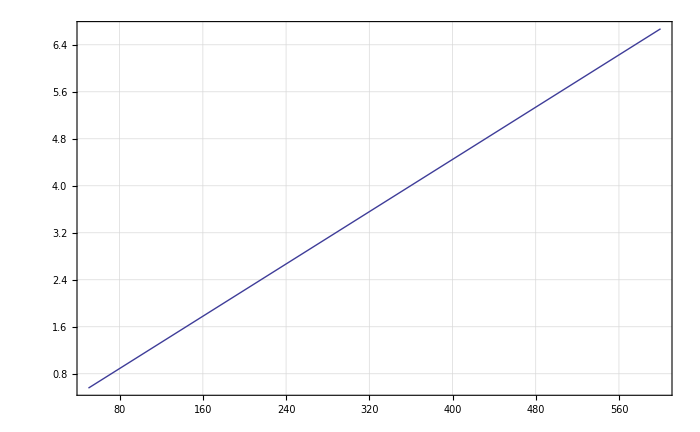

```mathematica
Plot[2*Pi*size/565,{size,50,600}]
```

```mathematica
(* CAbsPlot = Plot[CAbs[i Subscript[λ, 0]/(2π)], {i, .2, 4}, PlotStyle-> RGBColor[0,0,1],FrameLabel-> {"q = (2  π a)/λ_0", "C_Abs  (μm^2)"}]
```

```mathematica
(* CExtPlot = Plot[CExt[i Subscript[λ, 0]/(2π)], {i,.2,4}, PlotStyle-> RGBColor[0,0,0], FrameLabel-> {"q = (2  π a)/λ_0", "C_Ext  (μm^2)"}]
```

```mathematica
(* CScatPlot = Plot[CScat[i Subscript[λ, 0]/(2π)], {i,.2,4}, PlotStyle-> RGBColor[0,0,0], FrameLabel-> {"q = (2  π a)/λ_0", "C_Scat  (μm^2)"}]
```

All three on the same plot.  The first cell creates a legend for the plot.

```mathematica
(* Plot[{CExt[i Subscript[λ, 0]/(2π)],CAbs[i Subscript[λ, 0]/(2π)],CScat[i Subscript[λ, 0]/(2π)]}, {i, .8,4}, PlotStyle-> RGBColor[0,0,0], FrameLabel-> {"q = (2  π a)/λ_0", "C_Ext  (μm^2)"}]
```

```mathematica
(* CLegend = {{{RGBColor[1,0,0],"C_scat"},{RGBColor[0,0,1],"C_abs"},{RGBColor[0,0,0],"C_ext"}}, LegendPosition-> {-.55,0.3}, LegendSize-> {0.25,0.25}, LegendShadow-> {0,0}};
```

```mathematica
(* ShowLegend[Show[CScatPlot,CAbsPlot,CExtPlot, DisplayFunction-> Identity], CLegend,DisplayFunction-> $DisplayFunction ];
```

## Calculate and plot the efficiencies

The efficiencies are defined simply as the ratio of the cross sections to the geometrical cross sectional area of the scatterer.

```mathematica
QScat[a_]:=  CScat[a]/(π a^2)
QAbs[a_]:= CAbs[a]/(π a^2)
QExt[a_]:=CExt[a]/(π a^2)
```

Print out efficiencies for the default parameters.

```mathematica
Print["Q_Scat = ",QScat[r]//N,"\nQ_Abs = ",QAbs[r]//N,"\nQ_Ext = ",QExt[r]//N ]
```

Q_Scat = 1.89254×10^-26
Q_Abs = 20.3321
Q_Ext = 20.3321

#### Linear plots of size parameter vs. efficiency.

Note that these plots take longer to generate as the size parameter increases.  The multiplicative factor in the argument converts the abscissa variable to q values (rather than radius values).

```mathematica
SetOptions[Plot, Frame-> True, PlotRange-> All, ImageSize-> 700, GridLines-> Automatic,PlotPoints-> 40];
```

```mathematica
(* QScatPlot = Plot[QScat[i (Subscript[λ, 0]/(2π) )], {i,.8, 4}, PlotStyle-> RGBColor[1,0,0],  FrameLabel-> {"q = (2  π a)/λ_0", "Q_Scat  (μm^2)"}]
```

```mathematica
(* QAbsPlot = Plot[QAbs[i (Subscript[λ, 0]/(2π))], {i, .8, 4}, PlotStyle-> RGBColor[0,0,1], FrameLabel-> {"q = (2  π a)/λ_0", "Q_Abs  (μm^2)"}]
```

```mathematica
(* QExtPlot =Plot[QExt[i Subscript[λ, 0]/(2π)], {i, .8, 4}, PlotStyle-> RGBColor[0,0,0], FrameLabel-> {"q = (2  π a)/λ_0", "Q_Ext  (μm^2)"}]
```

All three on the same plot.  The first cell creates a legend for the plot.

```mathematica
(* QLegend = {{{RGBColor[1,0,0],"Q_scat"},{RGBColor[0,0,1],"Q_abs"},{RGBColor[0,0,0],"Q_ext"}}, LegendPosition-> {-.55,0.3}, LegendSize-> {0.25,0.25}, LegendShadow-> {0,0}};
```

```mathematica
(* ShowLegend[Show[QScatPlot,QAbsPlot,QExtPlot, PlotRange-> All,DisplayFunction-> Identity], QLegend,DisplayFunction-> $DisplayFunction ];
```

#### Log-linear plots of size parameter vs. efficiency.

These plots are useful when plotting over a large range of q values, but take longer to generate as the size parameter increases.  The multiplicative factor in the argument converts the abscissa variable to q values (rather than radius values).

```mathematica
(* SetOptions[LogLinearPlot, Frame-> True, PlotRange-> All, ImageSize-> 700, GridLines-> Automatic,PlotPoints-> 40];
```

```mathematica
Note from Guy: These scattering efficiencies should be dimensionless but were not coded so by Art Lampado.  I will go through and alter this.
```

```mathematica
(* QScatLogPlot = LogLinearPlot[QScat[i (Subscript[λ, 0]/(2π) )], {i,.8, 6}, PlotStyle-> RGBColor[1,0,0],  AxesLabel-> {"q = (2  π a)/λ_0", "Q_Scat  (μm^2)"}]
```

```mathematica
(* QAbsLogPlot = LogLinearPlot[QAbs[i (Subscript[λ, 0]/(2π))], {i, .8, 6}, PlotStyle-> RGBColor[0,0,1], AxesLabel-> {"q = (2  π a)/λ_0", "Q_Abs  (μm^2)"}]
```

```mathematica
(* QExtLogPlot = LogLinearPlot[QExt[i Subscript[λ, 0]/(2π)], {i, .8, 6}, PlotStyle-> RGBColor[0,0,0], AxesLabel-> {"q = (2  π a)/λ_0", "Q_Ext  (μm^2)"}]
```

All three on the same plot.  The first cell creates a legend for the plot.

```mathematica
QLegend = {{{RGBColor[1,0,0],"Q_scat"},{RGBColor[0,0,1],"Q_abs"},{RGBColor[0,0,0],"Q_ext"}}, LegendPosition-> {-.55,0.3}, LegendSize-> {0.25,0.25}, LegendShadow-> {0,0}};
```

```mathematica
ShowLegend[Show[QScatLogPlot,QAbsLogPlot,QExtLogPlot, PlotRange-> All,DisplayFunction-> Identity], QLegend,DisplayFunction-> $DisplayFunction ];
```

Show::gcomb: Could not combine the graphics objects in Show[QScatLogPlot, QAbsLogPlot, QExtLogPlot, PlotRange → All, DisplayFunction → Identity].

## Calculate and plot the asymmetry factor

The equation for the asymmetry factor comes from Fu and Sun (Applied Optics, Vol. 40, No. 9, 2001, pp. 1354-1361).

```mathematica
g[a_] := (2∑_(l=1)^LastTerm[a] ((l(l+2))/(l + 1) Re[(an[l,a]*  SuperStar[an[l+1,a]]+ bn[l,a]*SuperStar[bn[l+1,a]])] + (2l+1)/(l(l + 1)) Re[(an[l,a] *SuperStar[bn[l,a]])]))/(∑_(l=1)^LastTerm[a] (2l+1)((Abs[an[l,a]])^2 + (Abs[bn[l,a]])^2))
```

```mathematica
StringJoin["The anisotropy value is g = ", ToString[-g[r]//N]]
```

The anisotropy value is g =           -10
2.05203 10

#### Create plot of size parameter vs. asymmetry factor.

```mathematica
The assummetry factor denotes the symmetry of the phase function and related whether forward scattering or back scattering is dominant (greater than 1 is forward, less than 1 is backscattering).
```

```mathematica
(* gPlot = Plot[g[i Subscript[λ, 0]/(2π)], {i,.8, 4}, Frame-> True, PlotRange-> All, ImageSize-> 700, PlotStyle-> RGBColor[1,0,0], GridLines-> Automatic, FrameLabel-> {"q = (2  π a)/λ_0", "Asymmetry Factor"}]
```

## Calculate and plot the albedo

The albedo is simply the ratio of the scattering to extinction cross sections.

```mathematica
albedo[a_] := CScat[a]/CExt[a];
StringJoin["The albedo is ", ToString[albedo[r]//N]]
```

The albedo is           -28
9.30814 10

```mathematica
albedo[r]
```

9.30814×10^-28

```mathematica
Manipulate[N[albedo[i*Subscript[λ, 0]/(2π)],3],{i,1,6}]
```

#### Create plot of albedo vs. size parameter.

```mathematica
(* SetOptions[LogLinearPlot, Frame-> True, PlotRange-> All, ImageSize-> 700, GridLines-> Automatic,PlotPoints-> 40];
```

```mathematica
(* In the next section of code, i is the size paramater.  *)
```

```mathematica
(* AlbedoPlot = LogLinearPlot[albedo[i Subscript[λ, 0]/(2π)], {i,.2, 6}, Frame-> True, PlotRange-> All, ImageSize-> 700, PlotStyle-> RGBColor[1,0,0], GridLines-> Automatic, FrameLabel-> {"q = (2  π a)/λ_0", "Albedo"}]
```

## Calculate and plot the scattering phase functions

Next, we construct the formulae for intensity as a function of angular position for incident radiation polarized in either of the two linear orthogonal polarization states.  Begin by defining the amplitude matrix elements, S1(r, θ) and S2(r, θ) which simplify the form of the resulting phase function equations a little

```mathematica
S1[a_,θ_]:= ∑_(l=1)^LastTerm[a] ((2 l+1)/(l (l+1)))(an[l,a]pi[l,θ]+bn[l,a]  τ[l,θ]);
S2[a_,θ_]:= ∑_(l=1)^LastTerm[a] ((2 l+1)/(l (l+1)))( an[l,a] τ[l,θ]+bn[l,a]  pi[l,θ] );
```

```mathematica
(* Added by Guy *)
```

```mathematica
(* Look at the phase difference between the scattered beams A and B
```

```mathematica
(* N[(Re[S1[a,θ]]Im[S2[a,θ]]-Re[S2[a,θ]]Im[S1[a, θ]])/(Re[S1[a,θ]]Re[S2[a,θ]]+Im[S1[a,θ]]Im[S2[a, θ]]),3]
```

```mathematica
(*  θ1=ContourPlot[N[(Re[S1[a, θ]]Im[S2[a, θ]]-Re[S2[a, θ]]Im[S1[a, θ]])/(Re[S1[a, θ]]Re[S2[a, θ]]+Im[S1[a, θ]]Im[S2[a, θ]]),3],{a,0,1},{θ,0,.9π}]
```

```mathematica
Look at the scattering amplitude in the forward direction:
```

```mathematica
Cextfor=(Subscript[λ, 0]^2/Pi)*Re[S[1,0]]
```

(296527078849 Re[S[1,0]])/(1000000000000 π)

Here are the phase function equations.  The normalization factor (to insure ∫P(cos(θ))ⅆΩ =  1) is sometime used in the literature (e.g., Fu and Sun) and sometimes neglected (e.g Bohren and Huffman).  Therefore, two separate functions for the unpolarized scattering phase function are created and either one may be used.

```mathematica
Iperp[a_, θ_]:= (Abs[S1[a,θ]])^2;

Ipar[a_, θ_]:= (Abs[S2[a,θ]])^2;

Iunpol[a_, θ_]:= (Iperp[a, θ] + Ipar[a, θ])/2;

Norma[a_]:=∑_(l=1)^LastTerm[a] 2(l + 1)((Abs[an[l,a]])^2 + (Abs[bn[l,a]])^2)

IunpolNorm[a_, θ_]:= (Iperp[a, θ] + Ipar[a, θ])/Norma[a];
```

### Create plots of the phase functions.

#### Log-linear plots of scattered intensity vs. angle.

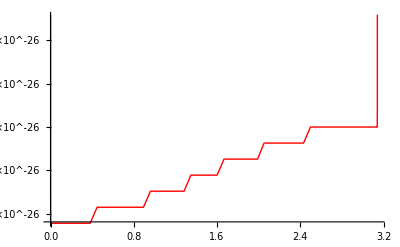

```mathematica
IPerpPlot = LogPlot[Evaluate[Iperp[r, θ]], {θ, 0, π},  PlotStyle-> RGBColor[1,0,0],  FrameLabel-> {"θ (deg)", "I_perp Phase Function"}]
```

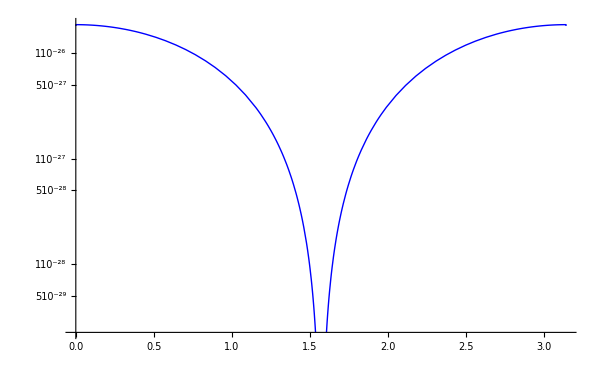

```mathematica
IParPlot = LogPlot[Evaluate[Ipar[r, θ]], {θ, 0, π},  PlotStyle-> RGBColor[0,0,1],  FrameLabel-> {"θ (deg)", "I_par Phase Function"}]
```

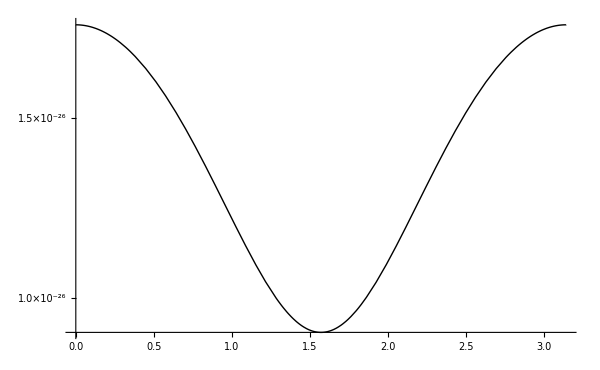

```mathematica
IUnpolPlot = LogPlot[Evaluate[Iunpol[r, θ]], {θ, 0, π},  PlotStyle-> RGBColor[0,0,0],  FrameLabel-> {"θ (deg)", "I_unpol Phase Function"}]
```

All three on the same plot.  The first expression creates a legend for the plot.

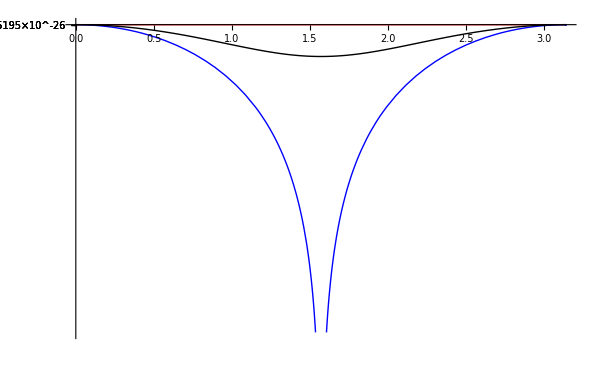

```mathematica
ILegend = {{{RGBColor[1,0,0],"I_perp"},{RGBColor[0,0,1],"I_par"},{RGBColor[0,0,0],"I_unpol"}}, LegendPosition-> {.5,0.3}, LegendSize-> {0.25,0.25}, LegendShadow-> {0,0}};
Show[IPerpPlot,IParPlot,IUnpolPlot, PlotRange-> All,DisplayFunction-> Identity, FrameLabel->{"θ (deg)", "Phase Functions"} ]
```

#### Polar plots of scattered intensity vs. angle.

Begin by defining some additional graphics to make the polar plots look good.  Note that when we normalize the phase functions to the peak value (which is the same for all polarization states), the maximum corresponds to θ = 0.   The PlotMax variable in the next cell permits the user to change the plot range, permitting "zooming" to look at the fine structure close to the particle.

```mathematica
Needs["NumericalCalculus`"]
```

```mathematica
MySpokes = Table[Graphics[Line[{{0,0},{Cos[θ Degree], Sin[θ Degree]}}]], {θ, 0, 345, 30}];
MyRings = Graphics[Table[{Dashing[{0.01,0.01}],Circle[{0,0},i]},{i,0,1,0.1}]];
NormFactor = NLimit[Iperp[r,ϕ], ϕ-> 0.01, WorkingPrecision-> 20,Terms->6];
```

```mathematica
N[NormFactor,3]
```

1.85195×10^-26

```mathematica
PlotMax = 1.025;
```

```mathematica
SetOptions[PolarPlot, Frame-> True, PlotRange-> All, ImageSize-> 500,  PlotPoints->30,  AspectRatio-> 1, FrameTicks-> None,PlotRange-> {{-PlotMax,PlotMax}, {-PlotMax,PlotMax}}, DisplayFunction-> Identity ];
```

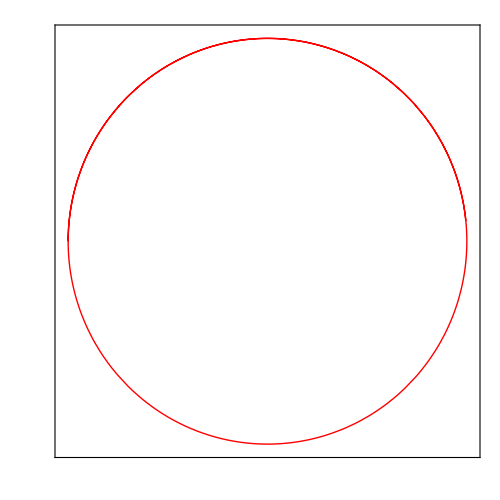

```mathematica
IPolarPerp = PolarPlot[Evaluate[Iperp[r,θ]/NormFactor], {θ,.1,3*Pi},PlotStyle-> RGBColor[1,0,0]]
```

I_parvs. θ

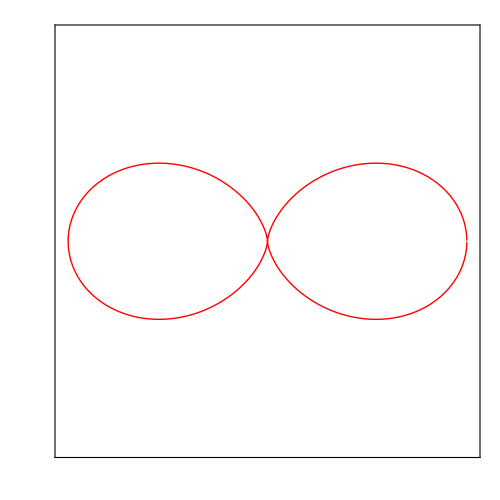

```mathematica
IPolarPar = PolarPlot[Evaluate[Ipar[r,θ]/NormFactor], {θ, π*.001,1.999π},PlotStyle-> RGBColor[1,0,0]]
```

I_unpolvs. θ

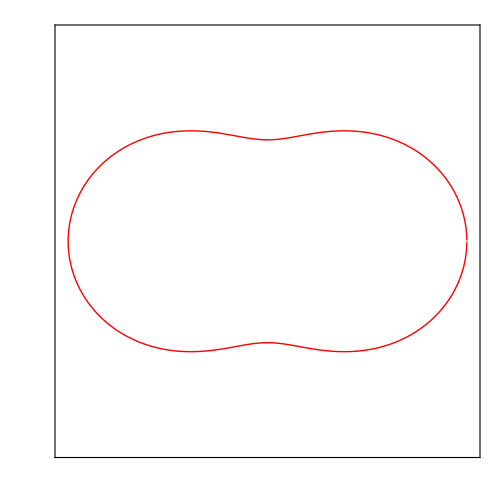

```mathematica
IPolarUnpol = PolarPlot[Evaluate[Iunpol[r,θ]/NormFactor], {θ, π*.001,1.999π},PlotStyle-> RGBColor[1,0,0]]
```

All three on the same plot.  The first expression creates a legend for the plot.

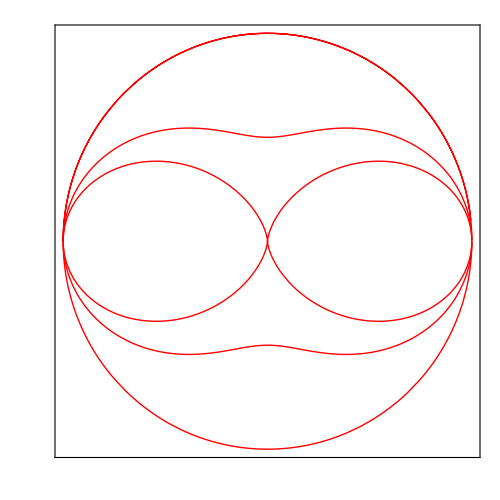

```mathematica
IPolarLegend = {{{RGBColor[1,0,0],"I_perp"},{RGBColor[0,0,1],"I_par"},{RGBColor[0,0,0],"I_unpol"}}, LegendPosition-> {.63,.6}, LegendSize-> {0.25,0.25}, LegendShadow-> {0,0}};
Show[IPolarPerp,IPolarPar,IPolarUnpol, PlotRange-> All,DisplayFunction-> Identity, FrameLabel->{None,None,"Normalized Phase Functions", None} ]
```

#### Log-polar plots of scattered intensity vs. angle.

Begin by defining a few labels and some additional graphics to make the polar plots look good.  Note that I normalize the phase functions to the peak value (which is the same for all polarization states and occurs in the forward direction where θ = 0).

```mathematica
MySpokes = Table[Graphics[Line[{{0,0},{Cos[θ Degree], Sin[θ Degree]}}]], {θ, 0, 345, 30}];
LogRings = Graphics[Table[{Dashing[{0.01,0.01}],Circle[{0,0},Log[10,i]]},{i,1.105171,10,1.1105171}]];
LogNormFactor = NLimit[Log[10,Iperp[r, ϕ]], ϕ-> 0.0, WorkingPrecision-> 20, Terms ->  6];
```

NLimit::noise: Cannot recognize a limiting value.  This may be due to  noise resulting from roundoff errors in which case higher WorkingPrecision,  fewer Terms, or a different Scale might help.

```mathematica
SetOptions[PolarPlot, Frame-> True, PlotRange-> All, ImageSize-> 500,  PlotPoints->30,  AspectRatio-> 1, FrameTicks-> None, Ticks-> None, DisplayFunction-> Identity ];
```

```mathematica
PerpMinValue = FindMinimum[Iperp[r, θ]/NormFactor, {θ,  .75π,π/2}]⟦2,1,2⟧;
ParMinValue = FindMinimum[Ipar[r, θ]/NormFactor, {θ,  .75π,π/2}]⟦2,1,2⟧;
UnpolMinValue = FindMinimum[Iunpol[r, θ]/NormFactor, {θ,  .75π,π/2}]⟦2,1,2⟧;
```

I_perpvs. θ

```mathematica
Timing[ILogPolarPerp = PolarPlot[Evaluate[Log[10,Iperp[r, θ]  + (1-Iperp[r, PerpMinValue])]/LogNormFactor], {θ, 0, 2π}, PlotStyle-> RGBColor[1,0,0], PlotRange-> {{-1,1}, {-1,1}}];]
```

General::ivar: -0.0253136 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

NLimit::noise: Cannot recognize a limiting value.  This may be due to  noise resulting from roundoff errors in which case higher WorkingPrecision,  fewer Terms, or a different Scale might help.

General::stop: Further output of NLimit :: noise will be suppressed during this calculation.

Power::infy: Infinite expression 1/√0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity encountered.

Infinity::indet: Indeterminate expression (0.  + 0.\ ⅈ)\ ComplexInfinity
 encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

{0.982,Null}

```mathematica
Show[ILogPolarPerp, MySpokes, LogRings,DisplayFunction-> $DisplayFunction];
```

I_parvs. θ

```mathematica
Timing[ILogPolarPar = PolarPlot[Evaluate[Log[10,Ipar[r, θ]  + (1-Ipar[r, ParMinValue])]/LogNormFactor], {θ, 0, 2π},  PlotStyle-> RGBColor[0,0,1], PlotRange-> {{-1,1}, {-1,1}}];]
```

General::ivar: 1.5708 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

NLimit::noise: Cannot recognize a limiting value.  This may be due to  noise resulting from roundoff errors in which case higher WorkingPrecision,  fewer Terms, or a different Scale might help.

General::stop: Further output of NLimit :: noise will be suppressed during this calculation.

Power::infy: Infinite expression 1/√0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity encountered.

Infinity::indet: Indeterminate expression (0.  + 0.\ ⅈ)\ ComplexInfinity
 encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

{0.983,Null}

```mathematica
Show[ILogPolarPar,  MySpokes, LogRings,DisplayFunction-> $DisplayFunction];
```

I_unpolvs. θ

```mathematica
Timing[ILogPolarUnPol = PolarPlot[Evaluate[Log[10,Iunpol[r, θ]  + (1-Iunpol[r, UnpolMinValue])]/LogNormFactor], {θ, 0, 2π}, PlotStyle-> RGBColor[0,0,0], PlotRange-> {{-1,1}, {-1,1}}];]
```

General::ivar: 1.5708 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

NLimit::noise: Cannot recognize a limiting value.  This may be due to  noise resulting from roundoff errors in which case higher WorkingPrecision,  fewer Terms, or a different Scale might help.

General::stop: Further output of NLimit :: noise will be suppressed during this calculation.

Power::infy: Infinite expression 1/√0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity encountered.

Infinity::indet: Indeterminate expression (0.  + 0.\ ⅈ)\ ComplexInfinity
 encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

{1.029,Null}

```mathematica
Show[ILogPolarUnPol, MySpokes, LogRings,DisplayFunction-> $DisplayFunction];
```

All three on the same plot.  The first expression creates a legend for the plot.

```mathematica
ILogPolarLegend = {{{RGBColor[1,0,0],"I_perp"},{RGBColor[0,0,1],"I_par"},{RGBColor[0,0,0],"I_unpol"}}, LegendPosition-> {.63,.6}, LegendSize-> {0.25,0.25}, LegendShadow-> {0,0}};
ShowLegend[Show[ILogPolarPerp,ILogPolarPar,ILogPolarUnPol,MySpokes, LogRings, PlotRange-> All,DisplayFunction-> Identity, FrameLabel->{None,None,"Log Phase Functions", None} ], ILogPolarLegend,DisplayFunction-> $DisplayFunction ];
```

## Calculate and plot the polarization ratio for unpolarized incident light

Note that this definition applies to an unpolarized incident beam.

```mathematica
PolRatio[a_, θ_]:=(Iperp[a, θ] - Ipar[a, θ])/(Iperp[a, θ] + Ipar[a, θ]);
```

Plot of the polarization ratio vs. angle

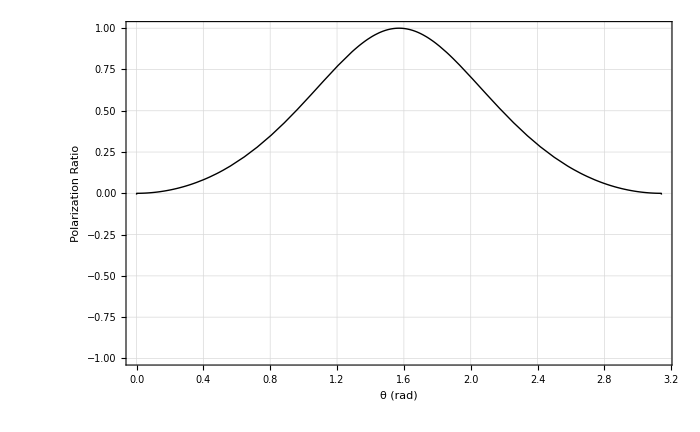

```mathematica
PolRatioPlot = Plot[Evaluate[PolRatio[r, θ]], {θ, 0, π}, Frame-> True, PlotRange-> {-1,1}, ImageSize-> 700, PlotStyle-> RGBColor[0,0,0], GridLines-> Automatic, FrameLabel-> {"θ (rad)","Polarization Ratio", "Polarization Ratio = I_perp/I_perp", None}]
```

## 3-D Plots

Here are some 3 dimensional plots of the phase functions.   These plots are handy because they reveal the asymmetry of the surfaces when a completely polarized input plane wave is incident.  The unpolarized case degenerates into a symmetric surface (about the optical axis).  This first few cells contain the amplitude matrix and intensity functions and were actually defined earlier for the 2D plots.  They are included here in case the cells for the 2D plots have not been evaluated.  Also included are the two possible normalizing factors for the unpolarized case (see above).

```mathematica
S1[a_, θ_]:= ∑_(l=1)^LastTerm[a] ((2 l+1)/(l (l+1)))(an[l,a]*pi[l,θ]+bn[l,a]*τ[l,θ])
S2[a_, θ_]:= ∑_(l=1)^LastTerm[a] ((2 l+1)/(l (l+1)))( an[l, a]*τ[l,θ]+bn[l,a]*pi[l,θ] )
```

```mathematica
S1[a_,θ_]:=( ∑_(l=1)^LastTerm[a] ((2 l+1)/(l (l+1)))(an[l,a]*pi[l,θ]+bn[l,a]* τ[l,θ1]))/.θ1-> θ;
S2[a_,θ_] :=( ∑_(l=1)^LastTerm[a] ((2 l+1)/(l (l+1)))( an[l,a]* τ[l,θ1]+bn[l,a]*pi[l,θ] ))/.θ1-> θ;
AmpMatrix[a_,θ_]:={{S2[a,θ],0},{0,S1[a,θ]}}
```

These are the 3D extensions of the intensity functions.  The ϕ dependence is on sin^2(ϕ) for the perpendicular case and on cos^2(ϕ) for the parallel case.

```mathematica
Iperp3D[a_,θ_,ϕ_]:= (Abs[S1[a,θ]] Sin[ϕ])^2
Ipar3D[a_,θ_,ϕ_]:= (Abs[S2[a,θ]] Cos[ϕ])^2
Iunpol3D[a_,θ_,ϕ_]:= (Iperp3D[a,θ,ϕ] + Ipar3D[a,θ,ϕ])/2
Norma2[a_]:=∑_(l=1)^LastTerm[a] 2(l + 1)((Abs[an[l,a]])^2 + (Abs[bn[l,a]])^2)
IunpolNorm3D[a_, θ_, ϕ_]:= (Iperp3D[a, θ, ϕ] + Ipar3D[a, θ, ϕ])/Norma2[a]
```

```mathematica
By integrating the scattering function for the unpolarized case, I can determine the total amount of scattered light within a certain angular region with respect to the particle.  Of particular region is the fraction of the scattered light that is inside the exit code.  This assumes that the light is normal to the interface and approaching a particle.
```

```mathematica
This can then be modified to deal with light approaching the particle from an angle and therefor the criticale angles will change.
```

Values required to center the particle at the origin.  Note there is no need to consider the ϕ dimension here so I use the 2D equations which evaluate more quickly.

```mathematica
Needs["NumericalCalculus`"]
```

```mathematica
NormFactor = NLimit[Iperp[r, ϕ], ϕ-> 0.01, WorkingPrecision-> 20, Terms ->  6]
LogNormFactor = NLimit[Log[10,Iperp[r, ϕ]], ϕ-> 0.01, WorkingPrecision-> 20, Terms ->  6]
```

1.85195×10^-26

-25.7324

```mathematica
PerpMinValue = FindMinimum[(Abs[S1[r,θ]])^2/NormFactor, {θ,  0.01,π}]
ParMinValue = FindMinimum[(Abs[S2[r,θ]])^2/NormFactor, {θ,  0.01,π}]
UnpolMinValue = FindMinimum[(Iperp[r, θ] + Ipar[r, θ])/(2 NormFactor), {θ,  0.01,π}]
```

{1.,{θ→0.01}}

{2.36881×10^-17,{θ→1.5708}}

{0.5,{θ→1.5708}}

```mathematica
PerpMinValue=.0453254;
PerpMinValue=.00683359;
UnpolMinValue=.0546361;
```

#### Plot the phase functions.

Start out by setting up the graphics.

```mathematica
SetOptions[SphericalPlot3D,BoxRatios->{1,1,1}, AspectRatio->1, Axes->True, PlotPoints->40,ViewPoint->{-15,0,0}, Boxed->False,ViewVertical->{0,1,0}, PlotRange-> All , LightSources->{{{1,0,1}, RGBColor[1,0,0]}, {{1,1,1},RGBColor[0,1,0]},{{0,1,1},RGBColor[0,0,1]},{{-1,0,-1},RGBColor[1,0,0]},{{-1,-1,-1},RGBColor[0,1,0]},{{0,-1,-1} ,RGBColor[0,0,1] }}];
```

SetOptions::optnf: LightSources is not a known option for SphericalPlot3D.

These next few cells can take long when the sampling is fine (i.e., when the PlotPoints value is set high).  Have patience.  Also, these plots will crash for angular values of exactly nπ (n = 0, ±1, ±2, ...).  I get around this by choosing plot ranges that only approach these values, rather than redefining the functions as their limiting values for all of these possible cases.  The latter approach, although more thorough, tends to extend the computation time substantially and adequate approximations can be made using the former by adding more digits (zeros or nines) to the arguments.  There are two plots for each phase function, a side view and an end view, and these are helpful in examining the asymmetry of the surfaces.  Start with the perpendicular phase function.

```mathematica
FullSimplify[S1[r,θ]]
```

(1.+0. ⅈ) ((-4.22829×10^-15+6.79116×10^-14 ⅈ)-(1.19452×10^-24+5.11565×10^-24 ⅈ) Cos[θ]+(4.22829×10^-15-6.79116×10^-14 ⅈ) Cos[2 θ]+(1.19452×10^-24+5.11565×10^-24 ⅈ) Cos[3 θ]+(9.5987×10^-35+7.05026×10^-34 ⅈ) Cos[4 θ]+(3.6705×10^-45+3.08421×10^-44 ⅈ) Cos[5 θ]+(8.32584×10^-56+7.42724×10^-55 ⅈ) Cos[6 θ]+(1.25746×10^-66+1.1598×10^-65 ⅈ) Cos[7 θ]+(1.35908×10^-77+1.28026×10^-76 ⅈ) Cos[8 θ]+(1.10433×10^-88+1.05579×10^-87 ⅈ) Cos[9 θ]+(6.99957×10^-100+6.7627×10^-99 ⅈ) Cos[10 θ]+(3.55852×10^-111+3.46688×10^-110 ⅈ) Cos[11 θ]+(1.48434×10^-122+1.45495×10^-121 ⅈ) Cos[12 θ]+(5.16796×10^-134+5.09182×10^-133 ⅈ) Cos[13 θ]+(1.5259×10^-145+1.51034×10^-144 ⅈ) Cos[14 θ]+(3.82826×10^-157+3.95684×10^-156 ⅈ) Cos[15 θ]) Csc[θ]^3 √(Sin[θ]^2)

```mathematica
FullSimplify[S2[r,θ]]
```

(1.+0. ⅈ) ((-1.70445×10^-24-2.48404×10^-23 ⅈ)-(2.11415×10^-15-3.39558×10^-14 ⅈ) Cos[θ]+(1.47626×10^-24+2.97101×10^-23 ⅈ) Cos[2 θ]+(2.11415×10^-15-3.39558×10^-14 ⅈ) Cos[3 θ]+(2.28194×10^-25-4.8697×10^-24 ⅈ) Cos[4 θ]+(1.26788×10^-35-2.99251×10^-34 ⅈ) Cos[5 θ]+(4.02693×10^-46-1.00107×10^-44 ⅈ) Cos[6 θ]+(8.17161×10^-57-2.09677×10^-55 ⅈ) Cos[7 θ]+(1.14584×10^-67-3.0036×10^-66 ⅈ) Cos[8 θ]+(1.17435×10^-78-3.12602×10^-77 ⅈ) Cos[9 θ]+(9.17152×10^-90-2.46985×10^-88 ⅈ) Cos[10 θ]+(5.63619×10^-101-1.53162×10^-99 ⅈ) Cos[11 θ]+(2.79551×10^-112-7.6522×10^-111 ⅈ) Cos[12 θ]+(1.14236×10^-123-3.14573×10^-122 ⅈ) Cos[13 θ]+(3.91194×10^-135-1.08262×10^-133 ⅈ) Cos[14 θ]+(1.13875×10^-146-3.16482×10^-145 ⅈ) Cos[15 θ]) Csc[θ]^3 √(Sin[θ]^2)

```mathematica
FullSimplify[Iperp3D[r,b,c]]
```

1.85195×10^-26 Sin[c]^2

```mathematica
Simplify[Evaluate[Log[10,Iperp3D[r,θ,ϕ] +(1-Iperp3D[r,PerpMinValue,ϕ])]/LogNormFactor]]
```

-0.0168774 Log[1-1.85195×10^-26 Sin[ϕ]^2+2. Abs[1/((0.+0. ⅈ)+(1.+0. ⅈ) Sin[θ])^3((-2.98986×10^-15+4.80207×10^-14 ⅈ)-(8.44652×10^-25+3.61731×10^-24 ⅈ) Cos[θ]+(2.98986×10^-15-4.80207×10^-14 ⅈ) Cos[2 θ]+(8.44652×10^-25+3.61731×10^-24 ⅈ) Cos[3 θ]+(6.7873×10^-35+4.98528×10^-34 ⅈ) Cos[4 θ]+(2.59543×10^-45+2.18086×10^-44 ⅈ) Cos[5 θ]+(5.88726×10^-56+5.25185×10^-55 ⅈ) Cos[6 θ]+(8.89158×10^-67+8.20105×10^-66 ⅈ) Cos[7 θ]+(9.61013×10^-78+9.05277×10^-77 ⅈ) Cos[8 θ]+(7.80881×10^-89+7.46558×10^-88 ⅈ) Cos[9 θ]+(4.94944×10^-100+4.78195×10^-99 ⅈ) Cos[10 θ]+(2.51625×10^-111+2.45146×10^-110 ⅈ) Cos[11 θ]+(1.04959×10^-122+1.0288×10^-121 ⅈ) Cos[12 θ]+(3.6543×10^-134+3.60046×10^-133 ⅈ) Cos[13 θ]+(1.07897×10^-145+1.06797×10^-144 ⅈ) Cos[14 θ]+(2.70699×10^-157+2.79791×10^-156 ⅈ) Cos[15 θ]) Sin[θ]]^2 Sin[ϕ]^2]

```mathematica
Simplify[Re[Evaluate[Log[10,Iperp3D[r,θ,ϕ] +(1-Iperp3D[r,PerpMinValue,ϕ])]/LogNormFactor]]]
```

-0.0168774 Re[Log[1-1.85195×10^-26 Sin[ϕ]^2+2. Abs[(((-2.98986×10^-15+4.80207×10^-14 ⅈ)-(8.44652×10^-25+3.61731×10^-24 ⅈ) Cos[θ]+(2.98986×10^-15-4.80207×10^-14 ⅈ) Cos[2 θ]+(8.44652×10^-25+3.61731×10^-24 ⅈ) Cos[3 θ]+(6.7873×10^-35+4.98528×10^-34 ⅈ) Cos[4 θ]+(2.59543×10^-45+2.18086×10^-44 ⅈ) Cos[5 θ]+(5.88726×10^-56+5.25185×10^-55 ⅈ) Cos[6 θ]+(8.89158×10^-67+8.20105×10^-66 ⅈ) Cos[7 θ]+(9.61013×10^-78+9.05277×10^-77 ⅈ) Cos[8 θ]+(7.80881×10^-89+7.46558×10^-88 ⅈ) Cos[9 θ]+(4.94944×10^-100+4.78195×10^-99 ⅈ) Cos[10 θ]+(2.51625×10^-111+2.45146×10^-110 ⅈ) Cos[11 θ]+(1.04959×10^-122+1.0288×10^-121 ⅈ) Cos[12 θ]+(3.6543×10^-134+3.60046×10^-133 ⅈ) Cos[13 θ]+(1.07897×10^-145+1.06797×10^-144 ⅈ) Cos[14 θ]+(2.70699×10^-157+2.79791×10^-156 ⅈ) Cos[15 θ]) Sin[θ])/((0.+0. ⅈ)+(1.+0. ⅈ) Sin[θ])^3]^2 Sin[ϕ]^2]]

```mathematica
SphericalPlotPerp = SphericalPlot3D[Evaluate[Log[10,Iperp3D[r,θ,ϕ]+(1-Iperp3D[r,PerpMinValue,ϕ])]/LogNormFactor], {θ, 0.1,1.9π}, {ϕ,0.1 , 1.9π},DisplayFunction->Identity,WorkingPrecision->4,MaxRecursion->1]
```

SphericalPlot3D::precw: The precision of the argument function ({Im[-1.85195×10^-26\ Sin[ϕ]^2 + Abs[Plus[« 13 »]]^2\ Sin[ϕ]^2] - 0, -Im[Cos[θ]^2] - 0, -Im[Cos[θ]^2] - 0, -Im[Cos[θ]^2] - 0, -Im[Cos[θ]^2] - 0, -Im[Cos[θ]^2] - 0, -Im[Cos[θ]^2] - 0, -Im[Cos[θ]^2] - 0, -Im[Cos[θ]^2] - 0, -Im[Cos[θ]^2] - 0, -Im[Cos[θ]^2] - 0, -Im[Cos[θ]^2] - 0, -Im[Cos[θ]^2] - 0, -Im[Cos[θ]^2] - 0, « 12 », -Im[Cos[θ]^2] - 0, -Im[Cos[θ]^2] - 0, -Im[Cos[θ]^2] - 0, -Im[Cos[θ]^2] - 0, -Im[Cos[θ]^2] - 0, -Im[Cos[θ]^2] - 0, -Im[Cos[θ]^2] - 0, -Im[Cos[θ]^2] - 0, -Im[Cos[θ]^2] - 0, -Im[Cos[θ]^2] - 0, -Im[Cos[θ]^2] - 0, -Im[Cos[θ]^2] - 0, -Im[Cos[θ]^2] - 0}) is less than WorkingPrecision (4.).

SphericalPlot3D::precw: The precision of the argument function ({1 + Re[-1.85195×10^-26\ Sin[« 1 »]^2 + Abs[« 1 »]^2\ Sin[« 1 »]^2] ≤ 0, 1 - Re[Cos[θ]^2] ≤ 0, 1 - Re[Cos[θ]^2] ≤ 0, 1 - Re[Cos[θ]^2] ≤ 0, 1 - Re[Cos[θ]^2] ≤ 0, 1 - Re[Cos[θ]^2] ≤ 0, 1 - Re[Cos[θ]^2] ≤ 0, 1 - Re[Cos[θ]^2] ≤ 0, 1 - Re[Cos[θ]^2] ≤ 0, 1 - Re[Cos[θ]^2] ≤ 0, 1 - Re[Cos[θ]^2] ≤ 0, 1 - Re[Cos[θ]^2] ≤ 0, 1 - Re[Cos[θ]^2] ≤ 0, « 14 », 1 - Re[Cos[θ]^2] ≤ 0, 1 - Re[Cos[θ]^2] ≤ 0, 1 - Re[Cos[θ]^2] ≤ 0, 1 - Re[Cos[θ]^2] ≤ 0, 1 - Re[Cos[θ]^2] ≤ 0, 1 - Re[Cos[θ]^2] ≤ 0, 1 - Re[Cos[θ]^2] ≤ 0, 1 - Re[Cos[θ]^2] ≤ 0, 1 - Re[Cos[θ]^2] ≤ 0, 1 - Re[Cos[θ]^2] ≤ 0, 1 - Re[Cos[θ]^2] ≤ 0, 1 - Re[Cos[θ]^2] ≤ 0}) is less than WorkingPrecision (4.).

-Graphics3D-

```mathematica
SideViewPerp = Show[SphericalPlotPerp,DisplayFunction-> $DisplayFunction,PlotPoints->80,]
```

Show::gcomb: Could not combine the graphics objects in ….

Show[-Graphics3D-,DisplayFunction→Identity,PlotPoints→80,Null]

```mathematica
(* EndOnViewPerp = Show[SphericalPlotPerp,DisplayFunction-> $DisplayFunction,ViewPoint->{0,0, -15}]
```

Plot the parallel phase function.  The same warnings as the last plot apply here.

```mathematica
SphericalPlotPar = SphericalPlot3D[Evaluate[Log[10,Ipar3D[r, θ, ϕ]  + (1-Ipar3D[r, ParMinValue, ϕ])]/LogNormFactor], {θ, 0.0001,1.99999π}, {ϕ,0.0001 , 1.99999π},DisplayFunction-> Identity]
```

Power::infy: Infinite expression 1/√0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity encountered.

-Graphics3D-

```mathematica
SideViewPar = Show[SphericalPlotPar,DisplayFunction-> $DisplayFunction, PlotRange-> All]
```

-Graphics3D-

```mathematica
EndOnViewPar = Show[SphericalPlotPar,DisplayFunction-> $DisplayFunction, PlotRange-> All,ViewPoint->{0, 0, -15}]
```

-Graphics3D-

Plot the unpolarized phase function.  The same warnings as the first plot also apply here.

```mathematica
SphericalPlotUnpol = SphericalPlot3D[Evaluate[Log[10,Iunpol3D[r, θ, ϕ]  + (1-Iunpol3D[r, UnpolMinValue, ϕ])]/LogNormFactor], {θ, 0.0001,1.99999π}, {ϕ,0.0001 , 1.99999π},DisplayFunction-> Identity,WorkingPrecision->30]
```

SphericalPlot3D::precw: The precision of the argument function ({Im[1/2\ (-1.84642×10^-26\ Power[« 2 »] - 1.85195×10^-26\ Power[« 2 »]) + 1/2\ (Power[« 2 »]\ Power[« 2 »] + Power[« 2 »]\ Power[« 2 »])] - 0, -Im[Cos[θ]^2] - 0, -Im[Cos[θ]^2] - 0, -Im[Cos[θ]^2] - 0, -Im[Cos[θ]^2] - 0, -Im[Cos[θ]^2] - 0, -Im[Cos[θ]^2] - 0, -Im[Cos[θ]^2] - 0, -Im[Cos[θ]^2] - 0, -Im[Cos[θ]^2] - 0, -Im[Cos[θ]^2] - 0, -Im[Cos[θ]^2] - 0, « 28 », -Im[Cos[θ]^2] - 0, -Im[Cos[θ]^2] - 0, -Im[Cos[θ]^2] - 0, -Im[Cos[θ]^2] - 0, -Im[Cos[θ]^2] - 0, -Im[Cos[θ]^2] - 0, -Im[Cos[θ]^2] - 0, -Im[Cos[θ]^2] - 0, -Im[Cos[θ]^2] - 0, -Im[Cos[θ]^2] - 0, « 27 »}) is less than WorkingPrecision (30.).

SphericalPlot3D::precw: The precision of the argument function ({1 + Re[1/2\ (Times[« 2 »] + Times[« 2 »]) + 1/2\ (Times[« 2 »] + Times[« 2 »])] ≤ 0, 1 - Re[Cos[θ]^2] ≤ 0, 1 - Re[Cos[θ]^2] ≤ 0, 1 - Re[Cos[θ]^2] ≤ 0, 1 - Re[Cos[θ]^2] ≤ 0, 1 - Re[Cos[θ]^2] ≤ 0, 1 - Re[Cos[θ]^2] ≤ 0, 1 - Re[Cos[θ]^2] ≤ 0, 1 - Re[Cos[θ]^2] ≤ 0, 1 - Re[Cos[θ]^2] ≤ 0, 1 - Re[Cos[θ]^2] ≤ 0, 1 - Re[Cos[θ]^2] ≤ 0, 1 - Re[Cos[θ]^2] ≤ 0, « 25 », 1 - Re[Cos[θ]^2] ≤ 0, 1 - Re[Cos[θ]^2] ≤ 0, 1 - Re[Cos[θ]^2] ≤ 0, 1 - Re[Cos[θ]^2] ≤ 0, 1 - Re[Cos[θ]^2] ≤ 0, 1 - Re[Cos[θ]^2] ≤ 0, 1 - Re[Cos[θ]^2] ≤ 0, 1 - Re[Cos[θ]^2] ≤ 0, 1 - Re[Cos[θ]^2] ≤ 0, 1 - Re[Cos[θ]^2] ≤ 0, 1 - Re[Cos[θ]^2] ≤ 0, 1 - Re[Cos[θ]^2] ≤ 0, « 27 »}) is less than WorkingPrecision (30.).

-Graphics3D-

```mathematica
SideViewUnpol = Show[SphericalPlotUnpol,DisplayFunction-> $DisplayFunction, PlotRange-> All];
```

```mathematica
EndOnViewUnpol = Show[SphericalPlotUnpol,DisplayFunction-> $DisplayFunction, PlotRange-> All,ViewPoint->{0, 0, -15}];
```

## Amplitude scattering matrix and Mueller matrix

The off diagonal elements of the amplitude scattering matrix for a spherical scatterer go to zero so we simply need to determine S_1(r,θ) and S_2(r, θ).  This has been done already in the phase function sections above and these function have simply been copied from there.

```mathematica
S1[a_,θ_]:=( ∑_(l=1)^LastTerm[a] ((2 l+1)/(l (l+1)))(an[l,a]*pi[l,θ]+bn[l,a]* τ[l,θ1]))/.θ1-> θ;
S2[a_,θ_] :=( ∑_(l=1)^LastTerm[a] ((2 l+1)/(l (l+1)))( an[l,a]* τ[l,θ1]+bn[l,a]*pi[l,θ] ))/.θ1-> θ;
AmpMatrix[a_,θ_]:={{S2[a,θ],0},{0,S1[a,θ]}}
```

Display the amplitude scattering matrix for light in the forward direction.

```mathematica
(OnAxisScatteringMatrix = AmpMatrix[r,0.000001])//Chop//MatrixForm
```

(0 | 0
0 | 0)

#### Mueller matrix

The Mueller matrix elements may be obtained from the amplitude scattering matrix.  The relationships used here come from Bohren and Huffman's text.  Using the fact that S_3(r, θ) = S_4(r, θ) = 0 simplifies things substantially.  We are left with 8 nonzero elements, only 3 of which are independent.  I prefer the usual Mueller matrix notation, representing each element as m_ijwhere i and j range from 0 to 3.   That is;

			M = (m_00 | m_10 | m_20 | m_30
m_10 | m_11 | m_12 | m_13
m_20 | m_21 | m_22 | m_23
m_30 | m_31 | m_32 | m_33)
					
In that case, the elements are defined as follows;

```mathematica
m00[a_, θ_] := 1/2((Abs[S1[a,θ]])^2+ (Abs[S2[a,θ]])^2)
m01[a_, θ_] := 1/2((Abs[S2[a,θ]])^2- (Abs[S1[a,θ]])^2)
m10[a_, θ_] := m01[a, θ]
m11[a_, θ_] := m00[a, θ]

m22[a_, θ_] := 1/2(SuperStar[S2[a,θ]] S1[a,θ]+ S2[a,θ] SuperStar[S1[a,θ]])
m23[a_, θ_] := 1/2(SuperStar[S2[a,θ]] S1[a,θ]- S2[a,θ] SuperStar[S1[a,θ]])
m32[a_, θ_] := -m23[a, θ]
m33[a_, θ_] := m22[a, θ]

m02[a_, θ_]=0; m03[a_, θ_]=0;m12[a_, θ_]=0;m13[a_, θ_]=0;
m20[a_, θ_]=0; m21[a_, θ_]=0;m30[a_, θ_]=0;m31[a_, θ_]=0;
```

```mathematica
MuellerMatrix[a_, θ_] := {{m00[a,θ], m01[a,θ], m02[a,θ], m03[a,θ]},{m10[a,θ], m11[a,θ], m12[a,θ], m13[a,θ]},{m20[a,θ], m21[a,θ], m22[a,θ], m23[a,θ]},{m30[a,θ], m31[a,θ], m32[a,θ], m33[a,θ]}}
```

```mathematica
(AxialMM = MuellerMatrix[r,0.0000001])//Chop//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
NormalizedAxialMM = AxialMM/AxialMM⟦1,1⟧//Chop//MatrixForm
```

(1. | 0.000799597 | 0 | 0
0.000799597 | 1. | 0 | 0
0 | 0 | 1. | 0
0 | 0 | 0 | 1.)

```mathematica
Interrupt[]
```

$Aborted

## Coated Sphere.

### Note that this code has not been written to account for the possibility of an absorbing external medium. As well, it does not include all of the plots generated for the uncoated case. These can be created in an analogous fashion to the ones generated in that case.

This section considers scattering by a spherical core particle with a uniform shell around, and in contact with it.  To start, we're going to need the optical and geometrical parameters of the core, coating, and external medium.   We next must calculate the relative indices, the size parameters of the core and the coating, and finally the final term taken in the series solution.  Note that all parameters which have analogies in the homogeneous sphere case above now have a "c" tacked onto their name to indicate this is a "coated sphere" calculation.  This way, the old variables remain for later comparison between the two cases.

### Enter known parameters.

The parameters used here correspond roughly to a spherical human red blood cell with a 7 nm thick cell membrane surrounding it.

```mathematica
Subscript[λ, 0] = 0.632830 * 10^-6               (* vacuum wavelength in meters *)

Subscript[n, core] = 1.402530            (* Real part of refractive index of core *)
Subscript[n, coating] = 1.3630;             (* Real part of refractive index of coating *)
Subscript[n, outside]= 1            (* Real part of refractive index outside particle *)

Subscript[k, core] = 5.5430*10^-6          (* Extinction coefficient of core *)
Subscript[k, coating] = 5.5430*10^-8    (* Extinction coefficient of coating*)
Subscript[k, outside] = 0     (* Extinction coefficient outside particle *)


Subscript[λ, core] =Subscript[λ, 0]/(Subscript[n, core] + I Subscript[k, core])                   (* wavelength in core *)

Subscript[λ, coating] =Subscript[λ, 0]/(Subscript[n, coating] + I Subscript[k, coating])                   (* wavelength in coating *)
Subscript[λ, outside] =Subscript[λ, 0]/(Subscript[n, outside] + I Subscript[k, outside])          (* wavelength in external medium *)



a = 2.7`30 * 10^-6   ;                       (* Core radius in meters *)
b = 2.707`30 * 10^-6   ;                  (* Coating radius in meters *)


Subscript[m, 1] = (Subscript[n, core]+ I Subscript[k, core])/(Subscript[n, outside]+ I Subscript[k, outside])      (* Relative refractive index of core *)
Subscript[m, 2] = (Subscript[n, coating]+ I Subscript[k, coating])/(Subscript[n, outside]+ I Subscript[k, outside])     (* Relative refractive index of coating *)


Subscript[q, c1] = (2 π)/Subscript[λ, outside] a                                  (* Size parameter for core *)
Subscript[q, c2] = (2 π)/Subscript[λ, outside] b                                 (* Size parameter for coating *)
LastTermc = Ceiling[Subscript[q, c2] + 4 (Subscript[q, c2])^(1/3) +2]
```

6.3283×10^-7

1.40253

1

5.543×10^-6

5.543×10^-8

0

4.51206×10^-7-1.78323×10^-12 ⅈ

4.64292×10^-7-1.88817×10^-14 ⅈ

6.3283×10^-7

1.40253+5.543×10^-6 ⅈ

1.363+5.543×10^-8 ⅈ

26.8075

26.877

41

### Calculate series coefficients

```mathematica
Subscript[A, n][l_]:= (Subscript[m, 2] ψPrime [ l,Subscript[m, 1] Subscript[q, c1]] ψ[l,Subscript[m, 2] Subscript[q, c1]] - Subscript[m, 1] ψ[l,Subscript[m, 1] Subscript[q, c1]] ψPrime[ l,Subscript[m, 2] Subscript[q, c1]])/(Subscript[m, 2] ψPrime [ l,Subscript[m, 1] Subscript[q, c1]] χ[l,Subscript[m, 2] Subscript[q, c1]] - Subscript[m, 1] ψ[l,Subscript[m, 1] Subscript[q, c1]] χPrime[ l,Subscript[m, 2] Subscript[q, c1]])
Subscript[B, n][l_]:= (Subscript[m, 2] ψPrime [ l,Subscript[m, 2] Subscript[q, c1]] ψ[l,Subscript[m, 1] Subscript[q, c1]] - Subscript[m, 1] ψ[l,Subscript[m, 2] Subscript[q, c1]] ψPrime[ l,Subscript[m, 1] Subscript[q, c1]])/(Subscript[m, 2] χPrime [ l,Subscript[m, 2] Subscript[q, c1]] ψ[l,Subscript[m, 1] Subscript[q, c1]] - Subscript[m, 1] χ[l,Subscript[m, 2] Subscript[q, c1]] ψPrime[ l,Subscript[m, 1] Subscript[q, c1]])
Subscript[a, nc][l_] :=  (ψ[l,Subscript[q, c2]](ψPrime[ l,Subscript[m, 2] Subscript[q, c2]] - Subscript[A, n][l] χPrime[ l,Subscript[m, 2] Subscript[q, c2]]) - Subscript[m, 2] ψPrime[ l,Subscript[q, c2]](ψ[l,Subscript[m, 2] Subscript[q, c2]] - Subscript[A, n][l] χ[ l,Subscript[m, 2] Subscript[q, c2]]))/(ζ[l,Subscript[q, c2]](ψPrime[ l,Subscript[m, 2] Subscript[q, c2]] - Subscript[A, n][l] χPrime[ l,Subscript[m, 2] Subscript[q, c2]]) - Subscript[m, 2] ζPrime[ l,Subscript[q, c2]](ψ[l,Subscript[m, 2] Subscript[q, c2]] - Subscript[A, n][l] χ[ l,Subscript[m, 2] Subscript[q, c2]]))
Subscript[b, nc][l_] := (Subscript[m, 2] ψ[l,Subscript[q, c2]](ψPrime[ l,Subscript[m, 2] Subscript[q, c2]] - Subscript[B, n][l] χPrime[ l,Subscript[m, 2] Subscript[q, c2]]) -  ψPrime[ l,Subscript[q, c2]](ψ[l,Subscript[m, 2] Subscript[q, c2]] - Subscript[B, n][l] χ[ l,Subscript[m, 2] Subscript[q, c2]]))/(Subscript[m, 2] ζ[l,Subscript[q, c2]](ψPrime[ l,Subscript[m, 2] Subscript[q, c2]] - Subscript[B, n][l] χPrime[ l,Subscript[m, 2] Subscript[q, c2]]) - ζPrime[ l,Subscript[q, c2]](ψ[l,Subscript[m, 2] Subscript[q, c2]] - Subscript[B, n][l] χ[ l,Subscript[m, 2] Subscript[q, c2]]))
```

### Calculate the Cross Sections and Efficiencies

```mathematica
Subscript[C, Scatc] = N[Subscript[λ, outside]^2/(2π)∑_(l=1)^LastTermc   (2 l+1)((Abs[Subscript[a, nc][l]])^2 + (Abs[Subscript[b, nc][l]])^2),4];

Subscript[C, Extc] = N[Subscript[λ, outside]^2/(2π) Re[∑_(l=1)^LastTermc (2l+1) (Subscript[a, nc][l] + Subscript[b, nc][l])],4];

Subscript[C, Absc] = N[Subscript[C, Extc] - Subscript[C, Scatc],4];
```

```mathematica
Subscript[Q, Extc] = Subscript[C, Extc]/(π b^2);
Subscript[Q, Scatc] = Subscript[C, Scatc]/(π b^2)   ;
Subscript[Q, Absc] = Subscript[C, Absc]/(π b^2);
```

```mathematica
Print["C_Scat = ", Simplify[Subscript[C, Scatc]//N], "        Q_Scat = ",Subscript[Q, Scatc]//N , 
	  ,Sumplify[ Subscript[C, Extc]//N],"        SubscriptBox[Q,Ext\\\ \\\ ] = ",Simplify[Subscript[Q, Extc]//N ], 
	  , Simplify[Subscript[C, Absc]//N],"        SubscriptBox[Q,Abs\\\ \\\ ] = ",Simplify[Subscript[Q, Absc]//N ]];
```

$Aborted

### Calculate the anisotropy (i.e., the g factor)

See the section above for a homogeneous sphere for a description of this section.  Note that the anisotropy expression is the same as before except that now we use the new coefficients from the Mie series.

```mathematica
gc = 4/(Subscript[Q, Scatc] Subscript[q, c2]^2)(Re[∑_(l=1)^LastTermc (l(l+2))/(l + 1) (Subscript[a, nc][l]  SuperStar[Subscript[a, nc][l+1]]+ Subscript[b, nc][l] SuperStar[Subscript[b, nc][l+1]])] + Re[∑_(l=1)^LastTermc (2l+1)/(l(l + 1)) (Subscript[a, nc][l]  SuperStar[Subscript[b, nc][l]])]);
```

```mathematica
StringJoin["The anisotropy value is g = ", ToString[gc]]
```

«2067101»

### Calculate the Intensity distributions (i.e., phase functions) for the 2 orthogonal polarization states for subsequent plotting

```mathematica
Timing[IntensityParallelC[θ_, r_, ϕ_]:= Subscript[λ, outside]^2/(4 π^2 r^2)(Abs[∑_(l=1)^LastTermc ((2 l+1)/(l (l+1)))(Subscript[a, nc][l] τ[l, θ] +    Subscript[b, nc][l] pi[l, θ])])^2 * (Cos[ϕ])^2;

IntensityPerpendicularC[θ_, r_, ϕ_]= Subscript[λ, outside]^2/(4 π^2 r^2)(Abs[∑_(l=1)^LastTermc ((2 l+1)/(l (l+1)))(Subscript[a, nc][l] pi[l, θ] +    Subscript[b, nc][l] τ[l, θ])])^2* (Sin[ϕ])^2;]
```

{1.435,Null}

```mathematica
Timing[cIntParallelC = Compile[{θ, r, ϕ}, Evaluate[IntensityParallelC[θ, r, ϕ]]];
cIntPerpendicularC = Compile[{θ, r, ϕ}, Evaluate[IntensityPerpendicularC[θ, r, ϕ]]];]
```

{1.498,Null}

### Plot the phase function in log-polar format.

Generate lists of the phase function data for both polarizations and the average.  Then shift the data to center the plots on the axes.  The first cell here tales a long time to evaluate with an angular sampling of 0.1 degree and large size parameters (say > 100).  Increase the sampling increment to speed it up.

```mathematica
Timing[
parListNormC = Table[Log[10,cIntParallelC[θ Degree,1.0,0]],{θ,0.000001,360, 0.1}];
  perListNormC = Table[Log[10,cIntPerpendicularC[θ Degree,1.0,π/2]] ,{θ ,0.000001,360,0.1}];
]
```

CompiledFunction::cfex: Could not complete external evaluation at instruction 8; proceeding with uncompiled evaluation.

General::stop: Further output of CompiledFunction :: cfex will be suppressed during this calculation.

{34.617,Null}

```mathematica
parPlotListC = parListNormC + Abs[Min[parListNormC]];
perPlotListC = perListNormC + Abs[Min[perListNormC]];
avgPlotListC = (parPlotListC + perPlotListC)/2;
```

$Aborted

```mathematica
PeakC = Max[{Max[parPlotListC], Max[perPlotListC] }];
```

Normalize the data to the max value across all three lists and generate the plots

```mathematica
avgPhaseFunctionC = PolarListPlot[avgPlotListC/PeakC,PlotJoined->True, AspectRatio->1, PlotPoints->60, PlotStyle->RGBColor[0,0,0], Axes->True, DisplayFunction->Identity];
ParPhaseFunctionC = PolarListPlot[parPlotListC/PeakC,PlotJoined->True, PlotPoints->60, PlotStyle->RGBColor[1,0,0], DisplayFunction->Identity];
PerpPhaseFunctionC = PolarListPlot[perPlotListC/PeakC,PlotJoined->True, PlotPoints->60, PlotStyle->RGBColor[0,0,1], DisplayFunction->Identity];
```

Set up the plot parameters and display normalized phase functions.  Note that the particle resides at the origin and the incident field is from the left side.

```mathematica
MyLabel3 = Graphics[Text[StyleForm["
StyleBox[\"Blue\",\nFontSize->11,\nFontColor->RGBColor[0, 0, 1]]
StyleBox[\":\",\nFontSize->11]
StyleBox[\" \",\nFontSize->11]
StyleBox[\"perpendicular\",\nFontSize->11]\n
StyleBox[\"Red\",\nFontSize->11,\nFontColor->RGBColor[1, 0, 0]]
StyleBox[\":\",\nFontSize->11]
StyleBox[\" \",\nFontSize->11]
StyleBox[\"parallel\",\nFontSize->11]\n
StyleBox[\"Black\",\nFontSize->11]
StyleBox[\":\",\nFontSize->11]
StyleBox[\" \",\nFontSize->11]
StyleBox[\"average\",\nFontSize->11] ", FontSize->12],{0.8, 0.875} ] ];
MyAxesLabel = Graphics[{Text[StyleForm["1", FontSize->16],{-0.05, 1} ] ,Text[StyleForm["10^-2", FontSize->16],{-0.075, 0.8} ],Text[StyleForm["10^-4", FontSize->16],{-0.075, 0.6} ], Text[StyleForm["10^-6", FontSize->16],{-0.075, 0.4} ]}];
```

```mathematica
MySpokes = Table[Graphics[Line[{{0,0},{Cos[θ Degree], Sin[θ Degree]}}]], {θ, 0, 345, 30}];
```

```mathematica
PagePlot = Show[{PerpPhaseFunctionC,ParPhaseFunctionC,avgPhaseFunctionC,MyLabel3,MyAxesLabel,MySpokes,Graphics[Table[{Dashing[{0.01,0.01}],Circle[{0,0},i]},{i,0,1,0.1}]],Graphics[Circle[{0,0},1]]}, AspectRatio->1, FrameTicks->None, Frame->True, PlotRange->{{-1,1},{-1,1}}, ImageSize->500, Ticks->None,FrameLabel->{None, None,None, None},DisplayFunction->$DisplayFunction];
```

Show::gcomb: Could not combine the graphics objects in ….

### Plot the phase function in log - linear format.

```mathematica
DataPeak = Max[{Max[cIntParallelC[0.000001,1.0,0]], Max[cIntParallelC[0.000001,1.0,π/2]]}];
```

```mathematica
MyTickLabels = Table[{i, ToString[i /Degree]}, {i, 0.0, π, π/12}];
```

```mathematica
MyLabel4 = Graphics[Text[StyleForm["
StyleBox[\"Blue\",\nFontSize->11,\nFontColor->RGBColor[0, 0, 1]]
StyleBox[\":\",\nFontSize->11]
StyleBox[\" \",\nFontSize->11]
StyleBox[\"perpendicular\",\nFontSize->11]\n
StyleBox[\"Red\",\nFontSize->11,\nFontColor->RGBColor[1, 0, 0]]
StyleBox[\":\",\nFontSize->11]
StyleBox[\" \",\nFontSize->11]
StyleBox[\"parallel\",\nFontSize->11]\n
StyleBox[\"Black\",\nFontSize->11]
StyleBox[\":\",\nFontSize->11]
StyleBox[\" \",\nFontSize->11]
StyleBox[\"average\",\nFontSize->11] ", FontSize->12],{2.1,-0.6} ] ];
```

Normalize the data to the max value across all three lists and generate the plots.  This cell takes a couple of minutes.

```mathematica
ParPhaseFunction3=Plot[Log[10,cIntParallelC[θ ,1,0]/DataPeak], {θ,0.00000001,π}, DisplayFunction-> Identity, PlotStyle-> RGBColor[1,0,0],PlotPoints->50];
PerPhaseFunction3=Plot[Log[10,cIntPerpendicularC[θ,1,π/2]/DataPeak],{θ,0.00000001,π}, DisplayFunction-> Identity, PlotStyle-> RGBColor[0,0,1],PlotPoints->50];
avgPhaseFunction3=Plot[Log[10,((cIntParallelC[θ ,1,0] + cIntPerpendicularC[θ ,1, π/2])/(2 DataPeak))],{θ,0,π},  DisplayFunction-> Identity, PlotStyle-> RGBColor[0,0,0],PlotPoints->50];
```

Display normalized phase functions where again, the particle resides at the origin and the incident field is from the left side.  Limit the plot range to examine the fine structure of the functions.

```mathematica
Show[{ParPhaseFunction3,PerPhaseFunction3,avgPhaseFunction3, MyLabel4}, DisplayFunction->$DisplayFunction, Frame->True,Axes->False,FrameLabel->{"θ (deg)","Log  [Normalized Intensity]"},DefaultFont->{"Times",10}, FrameTicks->{MyTickLabels, Automatic, None, None}, PlotRange->All, ImageSize->700, GridLines->{MyTickLabels, Automatic}];
```

## Spectral Calculations

### Note that this part of the code has not been updated to account for absorbing external media yet. It works for external media with known refractive index dispersion where the imaginary part is zero at all wavelengths. Of course the particle may have nonzero spectral absorption. Also, this section is not as extensive as the monochromatic case in terms of the number and breath of plots displayed (partially because the spectral calculations can take very long). Plots analogous to those for the monochromatic case can all be generated if desired, as can the spectral Mueller matrices, scattering matrices, etc. Finally, notice that you must choose one of two way to load the spectral data . The first way is to read the raw data from a file. In this case, interpolations to the data are generated and used for calculation of the spectral scattering properties. The second method is to directly load the interpolations from a file which was generated previously, and tends to be faster for large data sets.

### Obtain dispersion data from files.

#### First, set the directory to that containing the dispersion data files. Begin by loading up the dispersion data for the scatterer. The files are assumed to be ASCII format and to contain seven lines of header information followed by the data in triads of the form (λ, n, k). Different file formats will require modification of the ReadList[ ] call in the next cell. The wavelength units are assumed to be nm.

```mathematica
SetDirectory["c:\\Art\\Notebooks\\Scatterometer\\Mie Theory\\Dispersion Data"];
```

Read in the scatterer dispersion data.

```mathematica
MyStream = OpenRead["H2O Optical Constants.DAT"];
DataFileHeader==Read[MyStream, {String, String, String, String,String, String, String}]
ScattererDispersionData = ReadList[MyStream, {Number,Number,Number}];
Close[MyStream];
```

#### Once the data is loaded, it is transposed so that interpolating polynomials to the n(λ) and k(λ) data can be generated. These functions can then be used in subsequent calculations for any value of λ in the range. Note that high frequency structure in the dispersion data (e.g., noise) can cause a high order interpolating polynomial to oscillate between these points, resulting in bad (i.e, complex) values at certain wavelengths. This can be avoided by using a low order (e.g., linear or quadratic) piecewise interpolation, by simply lowering the InterpolationOrder option. For high resolution data, this should be an acceptable solution.

```mathematica
nScat = Interpolation[Transpose[Take[Transpose[ScattererDispersionData],2]], InterpolationOrder->3];
kScat = Interpolation[Transpose[Take[Transpose[ScattererDispersionData],{1,3,2}]], InterpolationOrder->3];
```

Plot it up to make sure all is well.

```mathematica
nPlots = Plot[nScat[λ], {λ, 200, 10000}, PlotStyle->{{RGBColor[1,0,0],Dashing[{0.01}]},{RGBColor[0,0,1], Dashing[{0.05}]}}, FrameLabel->{"wavelength (nm)", "n (unitless)", "n(λ)", None}, GridLines->Automatic,PlotRange->All,DisplayFunction->Identity];
kPlots = Plot[kScat[λ], {λ,200, 10000}, PlotRange->All, FrameLabel->{"wavelength (nm)", "k (unitless)", "k(λ)", None},GridLines->Automatic,DisplayFunction->Identity];
Show[GraphicsArray[{nPlots, kPlots}], DisplayFunction->$DisplayFunction, ImageSize->900];
```

Read in the medium data.  Same as above.

```mathematica
MyStream = OpenRead["Air Optical Constants2.dat"];
DataFileHeader==Read[MyStream, {String, String, String, String,String, String, String}]
MediumDispersionData = ReadList[MyStream, {Number, Number, Number}];
Close[MyStream];
```

Create a pair of interpolating functions for the medium data.

```mathematica
nMed = Interpolation[Transpose[Take[Transpose[MediumDispersionData],2]], InterpolationOrder->3]
kMed = Interpolation[Transpose[Take[Transpose[MediumDispersionData],{1,3,2}]], InterpolationOrder->3]
```

```mathematica
nPlots = Plot[nMed[λ], {λ, 200, 10000}, PlotStyle->{{RGBColor[1,0,0],Dashing[{0.01}]},{RGBColor[0,0,1], Dashing[{0.05}]}}, FrameLabel->{"wavelength (nm)", "n (unitless)", "n(λ)", None}, GridLines->Automatic,PlotRange->All,DisplayFunction->Identity];
kPlots = Plot[kMed[λ], {λ,200, 10000}, PlotRange->All, FrameLabel->{"wavelength (nm)", "k (unitless)", "k(λ)", None},GridLines->Automatic,DisplayFunction->Identity];
Show[GraphicsArray[{nPlots, kPlots}], DisplayFunction->$DisplayFunction, ImageSize->900];
```

#### Plot all of the interpolation functions to make sure all is well up to this point. Examine the plots showing the fits to the data to make sure the interpolations are reasonable.

```mathematica
RealPartDispersion = Plot[{nScat[λ],nMed[λ]}, {λ,200,10000},PlotStyle->{RGBColor[1,0,0], RGBColor[0,0,1]}, PlotRange->All, FrameLabel->{"λ (nm)", "n (unitless)", "n(λ) for \!\(\*
StyleBox[\"scatterer\",\nFontColor->RGBColor[1, 0, 0]]\) and \!\(\*
StyleBox[\"medium\",\nFontColor->RGBColor[0, 0, 1]]\)", None}, GridLines->Automatic,DisplayFunction->Identity];
ImaginaryPartDispersion = LogPlot[{kScat[λ], kMed[λ]}, {λ,200, 10000},PlotStyle->{RGBColor[1,0,0], RGBColor[0,0,1]}, PlotRange->Automatic, FrameLabel->{"λ (nm)", "k  (unitless)", "k(λ) for \!\(\*
StyleBox[\"scatterer\",\nFontColor->RGBColor[1, 0, 0]]\) and \!\(\*
StyleBox[\"medium\",\nFontColor->RGBColor[0, 0, 1]]\)", None}, GridLines->Automatic,DisplayFunction->Identity];

Show[GraphicsArray[{RealPartDispersion,ImaginaryPartDispersion }, DisplayFunction->$DisplayFunction], ImageSize->900];
```

### Obtain dispersion data from previously saved interpolating functions.

#### If you have already saved the interpolating functions approximating the dispersion data these may be loaded here. Don't forget to set the directory to that containing the interpolations file.

```mathematica
SetDirectory["c:\\Art\\Notebooks\\Scatterometer\\Mie Theory\\Dispersion Data"];
```

```mathematica
nScat  = Get["HbIndexInterpolations.m"]⟦2⟧;
kScat  = Get["HbIndexInterpolations.m"]⟦3⟧;
```

```mathematica
nMed  = Get["H2OIndexInterpolations.m"]⟦2⟧;
kMed  = Get["H2OIndexInterpolations.m"]⟦3⟧;
```

```mathematica
nPlots = Plot[{nScat[λ], nMed[λ]}, {λ, 400, 760}, PlotStyle->{{RGBColor[1,0,0],Dashing[{0.01}]},{RGBColor[0,0,1], Dashing[{0.05}]}}, FrameLabel->{"wavelength (nm)", "n (unitless)", "Plot of n vs. λ", None}, GridLines->Automatic,PlotRange->Automatic,DisplayFunction->Identity];
kPlots = LogPlot[{kScat[λ], kMed[λ]}, {λ,250, 1000}, PlotRange->Automatic, FrameLabel->{"wavelength (nm)", "n (unitless)", "Plot of k vs. λ", None},GridLines->Automatic,DisplayFunction->Identity];
Show[GraphicsArray[{nPlots, kPlots}], DisplayFunction->$DisplayFunction, ImageSize->900];
```

### Now define the a_n and b_n coefficients and the spectral cross sections. These are the same as those used in the monochromatic case except that the spectral nature of this calculation requires certain variables to be redefined as functions of λ. Namely, the relative refractive index and the q parameter. Also, the limit of the series that defines a_n and b_n depends on q so it too is recast to produce the correct number of series terms for each wavelength.

```mathematica
radius = 1 ;     (* units are μm *)
nRel[λ_] = (nScat[λ] + I kScat[λ])/(nMed[λ] + I kMed[λ]);

qSpec[λ_] = (2 π)/λ (nMed[λ] + I kMed[λ]) (radius * 1000) ;

MaxTerm[λ_]:=Ceiling[Re[qSpec[λ]] + 4 Re[qSpec[λ]^(1/3) ]+2]
```

Now, set up the Mie coefficient functions.

```mathematica
aCoeff[l_, λ_] :=( nRel[λ] ψPrime [ l,qSpec[λ]] ψ[l,nRel[λ] qSpec[λ]] - ψ[l,qSpec[λ]] ψPrime [ l,nRel[λ] qSpec[λ]])/(nRel[λ] ζPrime[l, qSpec[λ]] ψ[l, nRel[λ] qSpec[λ]] - ζ[l,qSpec[λ]] ψPrime[l, nRel[λ] qSpec[λ]]  );

bCoeff[l_, λ_] :=(nRel[λ] ψPrime [ l,nRel[λ] qSpec[λ]] ψ[l, qSpec[λ]] - ψ[l,nRel[λ] qSpec[λ]] ψPrime [ l,qSpec[λ]])/(nRel[λ]ζ[l,qSpec[λ]] ψPrime[l,nRel[λ] qSpec[λ]] - ζPrime[l, qSpec[λ]] ψ[l, nRel[λ] qSpec[λ]]);
```

Calculate the cross sections.

```mathematica
CScat[λ_]:= λ^2/(2 π (Abs[(nMed[λ] + I kMed[λ])])^2) ∑_(l=1)^MaxTerm[λ] (2l+1)((Abs[aCoeff[l, λ]])^2+(Abs[bCoeff[l, λ]])^2);  
CExt[λ_]:= λ^2/(2 π( Abs[(nMed[λ] + I kMed[λ])])^2)∑_(l=1)^MaxTerm[λ] (2l+1)Re[(aCoeff[l, λ]+bCoeff[l, λ])];  

CAbs[λ_]:=CExt[λ] - CScat[λ];
```

Compiling these functions seems to speed things up a little.

```mathematica
SpeedyCScat = Compile[{{ψ, _Real}}, CScat[ψ], {{CScat[_], _Real}}];
SpeedyCAbs = Compile[{{ψ, _Real}}, CAbs[ψ], {{CAbs[_], _Real}}];
SpeedyCExt = Compile[{{ψ, _Real}}, CExt[ψ], {{CExt[_], _Real}}];
```

### Plot up the spectral cross sections. The division by 10^6gets us back to units of μm^2. Note that these cells take a long time to evaluate.

```mathematica
Timing[Subscript[σ, s] = Table[{λ, SpeedyCScat[λ]/10^6}, {λ, 400, 1000, 1}];]
```

```mathematica
Subscript[σ, sPlot] = ListPlot[Subscript[σ, s],  PlotJoined->True,PlotRange->All,PlotStyle->RGBColor[1,0,0],  FrameLabel->{"λ (nm)", "σ_s (μm^2)", "Scattering cross section", None}, GridLines->Automatic, ImageSize-> 500];
```

```mathematica
Timing[Subscript[σ, a] = Table[{λ, SpeedyCAbs[λ]/10^6}, {λ, 400, 750, 1}];]
```

```mathematica
Subscript[σ, aPlot] =ListPlot[Subscript[σ, a],  PlotJoined->True,PlotRange->All,PlotStyle->RGBColor[0,0,1],  FrameLabel->{"λ (nm)", "σ_a (μm^2)", "Absorption cross section", None}, GridLines->Automatic, ImageSize-> 500];
```

```mathematica
Timing[Subscript[σ, ext] = Table[{λ, SpeedyCExt[λ]/10^6}, {λ, 200, 10000, 0.4}];]
```

```mathematica
Subscript[σ, extPlot] =ListPlot[Subscript[σ, ext],  PlotJoined->True,PlotRange->{{200, 10000},All}, FrameLabel->{"λ (nm)", "σ_ext (μm^2)", "Extinction cross section", None}, GridLines->Automatic, ImageSize-> 500];
```

### Plot up the spectral efficiencies.

```mathematica
Subscript[Q, s] = Transpose[Transpose[Subscript[σ, s]]/{1,π radius^2}];
```

```mathematica
Subscript[Q, sPlot] = ListPlot[Subscript[Q, s],  PlotJoined->True,PlotRange->All,PlotStyle->RGBColor[1,0,0], GridLines->Automatic, ImageSize-> 500,  FrameLabel->{"λ (nm)", "Q_s (unitless)"}];
```

```mathematica
Subscript[Q, a] = Transpose[Transpose[Subscript[σ, a]]/{1,π radius^2}];
```

```mathematica
Subscript[Q, aPlot] = ListPlot[Subscript[Q, a],  PlotJoined->True,PlotRange->All,PlotStyle->RGBColor[0,0,1],  FrameLabel->{"λ (nm)", "Q_a (unitless)", "Absorption  efficiency", None}, GridLines->Automatic, ImageSize-> 500];
```

```mathematica
Subscript[Q, ext] = Transpose[Transpose[Subscript[σ, ext]]/{1,π radius^2}];
```

```mathematica
Subscript[Q, extPlot] = LogLinearListPlot[Subscript[Q, ext],  PlotJoined->True,PlotRange->All, FrameLabel->{"λ (nm)", "Q_ext (unitless)", "Extinction efficiency", None}, GridLines->Automatic, ImageSize-> 500];
```

```mathematica
Test = Transpose[{1000(Transpose[Subscript[Q, ext]][[1]])^-1,Transpose[Subscript[Q, ext]][[2]]}];
```

```mathematica
Subscript[Q, extPlot2] = ListPlot[Test,  PlotJoined->True,PlotRange->{All, All}, FrameLabel->{"λ (nm)", "Q_ext (unitless)", "Extinction efficiency", None}, GridLines->Automatic, ImageSize-> 450, AspectRatio-> 1.25];
```

### Create interpolations to the results and export them.

#### Since the previous interpolating functions can take a long time to generate, here is some code to save them to file. They can then be read in short order as compared to having to regenerate them.

```mathematica
HbScatCrossSection = Interpolation[Subscript[σ, s]];
HbAbsCrossSection = Interpolation[Subscript[σ, a]];
HbExtCrossSection = Interpolation[Subscript[σ, ext]];
```

```mathematica
HbScatEfficiency = Interpolation[Subscript[Q, s]];
HbAbsEfficiency = Interpolation[Subscript[Q, a]];
HbExtEfficiency = Interpolation[Subscript[Q, ext]];
```

```mathematica
SetDirectory["C:\\Art\\Notebooks\\Scatterometer\\Mie Theory\\Dispersion Data"];
```

```mathematica
HbO2Header = "Interpolations of σ_s, σ_a, σ_ext, Q_s, Q_a, and Q_ext for oxygenated hemoglobin.";
HbHeader = "Interpolations of σ_s, σ_a, σ_ext, Q_s, Q_a, and Q_ext for deoxygenated hemoglobin.";
```

```mathematica
Put[{HbHeader,HbScatCrossSection, HbAbsCrossSection, HbExtCrossSection,HbScatEfficiency, HbAbsEfficiency, HbExtEfficiency }, "Hb XSections and Q Interpolations.m"]
```

$Aborted